# Comparison of DMS immune escape to MLR growth advantage

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/trvrb/Documents/src/ncov-escape/escape-mlr-comparison

## Colors

```mathematica
toHexString[n_Integer]:=StringJoin[ToString/@(IntegerDigits[n,16]/.Thread[Range[10,15]->CharacterRange["A","F"]])]
```

```mathematica
rgbColorToHex[rgbColor_]:="#"<>StringJoin[Map[toHexString[Round[#*255]]&,Level[rgbColor,1]]]
```

```mathematica
start[n_]:=0.07;
```

```mathematica
stop[n_]:=0.99;
```

```mathematica
gap[n_]:=(stop[n]-start[n])/(n-1)
```

```mathematica
makeColors[n_]:=Table[ColorData["Rainbow"][i],{i,start[n],stop[n],gap[n]}];
```

```mathematica
colors=Append[makeColors[6],Gray]
```

{RGBColor[0.30382016, 0.13051672, 0.67703096],RGBColor[0.26866900800000004, 0.492994304, 0.7985057680000001],RGBColor[0.4305106, 0.702073568, 0.5395238880000001],RGBColor[0.7003634240000002, 0.742645096, 0.30201920799999993],RGBColor[0.897113792, 0.5919722799999999, 0.218624288],RGBColor[0.86067868, 0.15704232000000004, 0.13666448],GrayLevel[0.5]}

```mathematica
legendPanel=SwatchLegend[colors,{"BA.2","BA.4","BA.5","BA.2.75","BQ.1","XBB","other"},LegendMarkerSize->11,LegendLayout->{"Column",1},Spacings->{0,1}]
```

```mathematica
colorRamp[t_]:=Blend[{GrayLevel[0.99],Lighter[ColorData["Rainbow"][0.75],0.4],Lighter[ColorData["Rainbow"][0.75],0.05],RGBColor[0.5807,0.6182,0.4944],Darker[ColorData["Rainbow"][0.3],0.05],Darker[ColorData["Rainbow"][0.3],0.4],GrayLevel[0.05]},t]
```

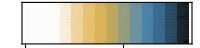

```mathematica
gaPanel=Rotate[DensityPlot[(x-0.5)/2,{x,0,2.5},{y,0,1},ColorFunction->colorRamp,ColorFunctionScaling->False,AspectRatio->0.1,PlotRangePadding->0,FrameTicks->{{None,None},{Automatic,None}}, ImageSize->200],Pi/2]
```

## Immune escape

```mathematica
escape=Import["../predictors/predictors.tsv","TSV"];
```

```mathematica
escapeHeader=escape[[1]]
```

{seqName,clade,Nextclade_pango,partiallyAliased,immune_escape,ace2_binding,rbd_count,non_rbd_spike_count,non_spike_count}

```mathematica
escapeHeaderRules=MapIndexed[#1->#2[[1]]&,escapeHeader]
```

{seqName→1,clade→2,Nextclade_pango→3,partiallyAliased→4,immune_escape→5,ace2_binding→6,rbd_count→7,non_rbd_spike_count→8,non_spike_count→9}

```mathematica
escape=Drop[escape,1];
```

```mathematica
escape=DeleteCases[escape,x_/;x[[2]]=="outgroup"];
```

```mathematica
Length[escape]
```

576

```mathematica
TableForm[escape,TableHeadings->{None,escapeHeader}]
```

seqName | clade | Nextclade_pango | partiallyAliased | immune_escape | ace2_binding | rbd_count | non_rbd_spike_count | non_spike_count
BA.2 | 21L (Omicron) | BA.2 | BA.2 | 0 | 0 | 0 | 0 | 2
XBG | recombinant | XBG | XBG | 0.601423 | 0.66973 | 4 | 5 | 13
XBF | recombinant | XBF | XBF | 0.836642 | 1.04277 | 7 | 9 | 14
XAN | recombinant | XAN | XAN | 0.386325 | 0.55831 | 3 | 6 | 11
XBD | recombinant | XBD | XBD | 0.633879 | 0.4677 | 6 | 10 | 15
XBE | recombinant | XBE | XBE | 0.601423 | 0.66973 | 4 | 6 | 11
XBA | recombinant | XBA | XBA | 0.315503 | 0.20216 | 4 | 9 | 41
XAJ | recombinant | XAJ | XAJ | 0.386325 | 0.35483 | 5 | 8 | 8
XAZ | recombinant | XAZ | XAZ | 0.386325 | 0.55831 | 3 | 6 | 11
XAV | recombinant | XAV | XAV | 0.386325 | 0.55831 | 3 | 6 | 12
XAS | recombinant | XAS | XAS | 0.386325 | 0.55831 | 3 | 6 | 8
XBC | recombinant | XBC | XBC | 0.326298 | 0.68716 | 4 | 14 | 45
XBC.2 | recombinant | XBC.2 | XBC.2 | 0.326298 | 0.68716 | 4 | 15 | 47
XBC.1 | recombinant | XBC.1 | XBC.1 | 0.528346 | 0.79272 | 5 | 14 | 47
XAY | recombinant | XAY | XAY | 0.528346 | 0.61445 | 4 | 12 | 29
XAY.2 | recombinant | XAY.2 | XAY.2 | 0.528346 | 0.61445 | 4 | 12 | 30
XAY.1 | recombinant | XAY.1 | XAY.1 | 0.528346 | 0.61445 | 4 | 13 | 32
XAY.1.1 | recombinant | XAY.1.1 | XAY.1.1 | 0.747425 | 0.72587 | 5 | 13 | 34
XBB | 22F (Omicron) | XBB | XBB | 0.907001 | 0.40687 | 9 | 9 | 12
XBB.2 | 22F (Omicron) | XBB.2 | XBB.2 | 0.907001 | 0.40687 | 9 | 10 | 12
XBB.5 | 22F (Omicron) | XBB.5 | XBB.5 | 0.907001 | 0.40687 | 9 | 10 | 13
XBB.4 | 22F (Omicron) | XBB.4 | XBB.4 | 0.979915 | 0.30641 | 10 | 9 | 13
XBB.4.1 | 22F (Omicron) | XBB.4.1 | XBB.4.1 | 1.02919 | 0.26628 | 11 | 10 | 14
XBB.3 | 22F (Omicron) | XBB.3 | XBB.3 | 0.907001 | 0.40687 | 9 | 9 | 14
XBB.3.1 | 22F (Omicron) | XBB.3.1 | XBB.3.1 | 0.907001 | 0.40687 | 9 | 10 | 14
XBB.1 | 22F (Omicron) | XBB.1 | XBB.1 | 0.907001 | 0.40687 | 9 | 10 | 13
XBB.1.2 | 22F (Omicron) | XBB.1.2 | XBB.1.2 | 0.907001 | 0.40687 | 9 | 11 | 13
XBB.1.1 | 22F (Omicron) | XBB.1.1 | XBB.1.1 | 0.907001 | 0.40687 | 9 | 10 | 14
XBB.1.3 | 22F (Omicron) | XBB.1.3 | XBB.1.3 | 0.983269 | 0.49564 | 10 | 10 | 13
XBB.1.4 | 22F (Omicron) | XBB.1.4 | XBB.1.4 | 0.907001 | 0.40687 | 9 | 11 | 13
XBB.1.5 | 22F (Omicron) | XBB.1.5 | XBB.1.5 | 0.907001 | 1.0124 | 9 | 10 | 13
BA.2.15 | 21L (Omicron) | BA.2.15 | BA.2.15 | -0.00009 | 0. | 0 | 5 | 8
BA.2.16 | 21L (Omicron) | BA.2.16 | BA.2.16 | -0.00009 | 0. | 0 | 4 | 10
BA.2.19 | 21L (Omicron) | BA.2.19 | BA.2.19 | -0.00009 | 0. | 0 | 4 | 8
BA.2.1 | 21L (Omicron) | BA.2.1 | BA.2.1 | -0.00009 | 0. | 0 | 4 | 9
BA.2.11 | 21L (Omicron) | BA.2.11 | BA.2.11 | 0.171804 | -0.04096 | 1 | 4 | 9
BA.2.18 | 21L (Omicron) | BA.2.18 | BA.2.18 | 0.047316 | 0.23107 | 1 | 4 | 8
BA.2.20 | 21L (Omicron) | BA.2.20 | BA.2.20 | -0.00009 | 0. | 0 | 5 | 10
BA.2.24 | 21L (Omicron) | BA.2.24 | BA.2.24 | 0.0131085 | -0.03172 | 1 | 4 | 8
BA.2.26 | 21L (Omicron) | BA.2.26 | BA.2.26 | -0.00009 | 0. | 0 | 4 | 10
BA.2.27 | 21L (Omicron) | BA.2.27 | BA.2.27 | -0.00009 | 0. | 0 | 4 | 9
BA.2.28 | 21L (Omicron) | BA.2.28 | BA.2.28 | -0.00009 | 0. | 0 | 4 | 11
BA.2.29 | 21L (Omicron) | BA.2.29 | BA.2.29 | -0.00009 | 0. | 0 | 4 | 9
BA.2.30 | 21L (Omicron) | BA.2.30 | BA.2.30 | -0.00009 | 0. | 0 | 4 | 10
BA.2.32 | 21L (Omicron) | BA.2.32 | BA.2.32 | -0.00009 | 0. | 0 | 4 | 9
BA.2.39 | 21L (Omicron) | BA.2.39 | BA.2.39 | -0.00009 | 0. | 0 | 5 | 11
BA.2.4 | 21L (Omicron) | BA.2.4 | BA.2.4 | -0.00009 | 0. | 0 | 4 | 9
BA.2.41 | 21L (Omicron) | BA.2.41 | BA.2.41 | -0.00009 | 0. | 0 | 5 | 8
BA.2.42 | 21L (Omicron) | BA.2.42 | BA.2.42 | -0.00009 | 0. | 0 | 5 | 9
BA.2.43 | 21L (Omicron) | BA.2.43 | BA.2.43 | 0.017546 | 0.11285 | 1 | 5 | 9
BA.2.46 | 21L (Omicron) | BA.2.46 | BA.2.46 | -0.00009 | 0. | 0 | 5 | 9
BA.2.48 | 21L (Omicron) | BA.2.48 | BA.2.48 | -0.00009 | 0. | 0 | 5 | 9
BA.2.50 | 21L (Omicron) | BA.2.50 | BA.2.50 | -0.00009 | 0. | 0 | 5 | 8
BA.2.5 | 21L (Omicron) | BA.2.5 | BA.2.5 | -0.00009 | 0. | 0 | 4 | 9
BA.2.54 | 21L (Omicron) | BA.2.54 | BA.2.54 | -0.00009 | 0. | 0 | 6 | 8
BA.2.55 | 21L (Omicron) | BA.2.55 | BA.2.55 | -0.00009 | 0. | 0 | 6 | 8
BA.2.58 | 21L (Omicron) | BA.2.58 | BA.2.58 | -0.00009 | 0. | 0 | 5 | 8
BA.2.59 | 21L (Omicron) | BA.2.59 | BA.2.59 | -0.00009 | 0. | 0 | 5 | 10
BA.2.60 | 21L (Omicron) | BA.2.60 | BA.2.60 | -0.00009 | 0. | 0 | 6 | 10
BA.2.62 | 21L (Omicron) | BA.2.62 | BA.2.62 | -0.00009 | 0. | 0 | 4 | 9
BA.2.63 | 21L (Omicron) | BA.2.63 | BA.2.63 | -0.00009 | 0. | 0 | 4 | 10
BA.2.61 | 21L (Omicron) | BA.2.61 | BA.2.61 | -0.00009 | 0. | 0 | 5 | 8
BA.2.65 | 21L (Omicron) | BA.2.65 | BA.2.65 | -0.00009 | 0. | 0 | 4 | 9
BA.2.64 | 21L (Omicron) | BA.2.64 | BA.2.64 | -0.00009 | 0. | 0 | 4 | 9
BA.2.70 | 21L (Omicron) | BA.2.70 | BA.2.70 | -0.00009 | 0. | 0 | 4 | 11
BA.2.77 | 21L (Omicron) | BA.2.77 | BA.2.77 | 0.380024 | 0.92132 | 4 | 7 | 12
BA.2.8 | 21L (Omicron) | BA.2.8 | BA.2.8 | -0.00009 | 0. | 0 | 4 | 9
BA.2.83 | 21L (Omicron) | BA.2.83 | BA.2.83 | 0.179303 | 1.12534 | 4 | 10 | 15
BA.2.82 | 21L (Omicron) | BA.2.82 | BA.2.82 | 0.215487 | 0.11142 | 1 | 5 | 10
BA.2.85 | 21L (Omicron) | BA.2.85 | BA.2.85 | -0.00009 | 0. | 0 | 5 | 9
BA.2.2 | 21L (Omicron) | BA.2.2 | BA.2.2 | -0.00009 | 0. | 0 | 5 | 10
BA.2.2.1 | 21L (Omicron) | BA.2.2.1 | BA.2.2.1 | -0.00009 | 0. | 0 | 5 | 11
BA.2.23.1 | 21L (Omicron) | BA.2.23.1 | BA.2.23.1 | -0.00009 | 0. | 0 | 4 | 12
BA.2.23 | 21L (Omicron) | BA.2.23 | BA.2.23 | -0.00009 | 0. | 0 | 4 | 9
BA.2.31.1 | 21L (Omicron) | BA.2.31.1 | BA.2.31.1 | -0.00009 | 0. | 0 | 5 | 9
BA.2.31 | 21L (Omicron) | BA.2.31 | BA.2.31 | -0.00009 | 0. | 0 | 4 | 9
BA.2.33 | 21L (Omicron) | BA.2.33 | BA.2.33 | -0.00009 | 0. | 0 | 4 | 9
BA.2.35 | 21L (Omicron) | BA.2.35 | BA.2.35 | 0.171804 | -0.04096 | 1 | 4 | 9
BA.2.40 | 21L (Omicron) | BA.2.40 | BA.2.40 | -0.00009 | 0. | 0 | 4 | 9
BA.2.40.1 | 21L (Omicron) | BA.2.40.1 | BA.2.40.1 | 0.047316 | 0.23107 | 1 | 4 | 9
BA.2.56 | 21L (Omicron) | BA.2.56 | BA.2.56 | 0.171804 | 0.10556 | 1 | 4 | 8
BA.2.56.1 | 21L (Omicron) | BA.2.56.1 | BA.2.56.1 | 0.171804 | 0.10556 | 1 | 6 | 8
BA.2.10 | 21L (Omicron) | BA.2.10 | BA.2.10 | -0.00009 | 0. | 0 | 4 | 9
BA.2.10.2 | 21L (Omicron) | BA.2.10.2 | BA.2.10.2 | -0.00009 | 0. | 0 | 4 | 10
BA.2.10.3 | 21L (Omicron) | BA.2.10.3 | BA.2.10.3 | -0.00009 | 0. | 0 | 5 | 9
BA.2.10.4 | 21L (Omicron) | BA.2.10.4 | BA.2.10.4 | 0.362464 | 0.73328 | 4 | 7 | 11
BA.2.10.1 | 21L (Omicron) | BA.2.10.1 | BA.2.10.1 | -0.00009 | 0. | 0 | 5 | 9
BJ.1 | 21L (Omicron) | BJ.1 | BA.2.10.1.1 | 0.571427 | 0.09519 | 7 | 11 | 14
BA.2.14 | 21L (Omicron) | BA.2.14 | BA.2.14 | -0.00009 | 0. | 0 | 5 | 8
BA.2.22 | 21L (Omicron) | BA.2.22 | BA.2.22 | -0.00009 | 0. | 0 | 5 | 9
BA.2.34 | 21L (Omicron) | BA.2.34 | BA.2.34 | -0.00009 | 0. | 0 | 4 | 9
BA.2.36 | 21L (Omicron) | BA.2.36 | BA.2.36 | -0.00009 | 0. | 0 | 5 | 8
BA.2.47 | 21L (Omicron) | BA.2.47 | BA.2.47 | -0.00009 | 0. | 0 | 6 | 9
BA.2.49 | 21L (Omicron) | BA.2.49 | BA.2.49 | -0.00009 | 0. | 0 | 4 | 9
BA.2.51 | 21L (Omicron) | BA.2.51 | BA.2.51 | -0.00009 | 0. | 0 | 5 | 8
BA.2.52 | 21L (Omicron) | BA.2.52 | BA.2.52 | -0.00009 | 0. | 0 | 4 | 9
BA.2.6 | 21L (Omicron) | BA.2.6 | BA.2.6 | -0.00009 | 0. | 0 | 4 | 9
BA.2.69 | 21L (Omicron) | BA.2.69 | BA.2.69 | -0.00009 | 0. | 0 | 4 | 9
BA.2.7 | 21L (Omicron) | BA.2.7 | BA.2.7 | -0.00009 | 0. | 0 | 4 | 9
BA.2.71 | 21L (Omicron) | BA.2.71 | BA.2.71 | -0.00009 | 0. | 0 | 5 | 8
BA.2.72 | 21L (Omicron) | BA.2.72 | BA.2.72 | -0.00009 | 0. | 0 | 5 | 8
BA.2.80 | 21L (Omicron) | BA.2.80 | BA.2.80 | 0.37993 | 0.10838 | 2 | 4 | 10
BA.2.81 | 21L (Omicron) | BA.2.81 | BA.2.81 | 0.171804 | 0.10556 | 1 | 4 | 9
BA.2.25 | 21L (Omicron) | BA.2.25 | BA.2.25 | -0.00009 | 0. | 0 | 4 | 9
BA.2.25.1 | 21L (Omicron) | BA.2.25.1 | BA.2.25.1 | -0.00009 | 0. | 0 | 4 | 10
BA.2.45 | 21L (Omicron) | BA.2.45 | BA.2.45 | 0.0675245 | -0.30756 | 1 | 4 | 8
BA.2.53 | 21L (Omicron) | BA.2.53 | BA.2.53 | 0.0675245 | -0.33553 | 1 | 4 | 9
BA.2.44 | 21L (Omicron) | BA.2.44 | BA.2.44 | 0.017546 | 0.11285 | 1 | 4 | 8
BA.2.13.1 | 21L (Omicron) | BA.2.13.1 | BA.2.13.1 | 0.171804 | 0.10556 | 1 | 5 | 9
BA.2.13 | 21L (Omicron) | BA.2.13 | BA.2.13 | 0.171804 | 0.10556 | 1 | 4 | 8
BA.2.9 | 21L (Omicron) | BA.2.9 | BA.2.9 | -0.00009 | 0. | 0 | 4 | 9
BA.2.9.3 | 21L (Omicron) | BA.2.9.3 | BA.2.9.3 | -0.00009 | 0. | 0 | 5 | 9
BA.2.9.4 | 21L (Omicron) | BA.2.9.4 | BA.2.9.4 | 0.215487 | 0.11142 | 1 | 4 | 10
BA.2.9.2 | 21L (Omicron) | BA.2.9.2 | BA.2.9.2 | -0.00009 | 0. | 0 | 4 | 10
BA.2.9.1 | 21L (Omicron) | BA.2.9.1 | BA.2.9.1 | 0.171804 | 0.10556 | 1 | 4 | 12
BA.2.9.5 | 21L (Omicron) | BA.2.9.5 | BA.2.9.5 | -0.00009 | 0. | 0 | 4 | 10
BA.2.9.6 | 21L (Omicron) | BA.2.9.6 | BA.2.9.6 | 0.171804 | 0.10556 | 1 | 4 | 11
BA.2.9.7 | 21L (Omicron) | BA.2.9.7 | BA.2.9.7 | -0.00009 | 0. | 0 | 5 | 13
BA.2.3 | 21L (Omicron) | BA.2.3 | BA.2.3 | -0.00009 | 0. | 0 | 4 | 10
BA.2.3.1 | 21L (Omicron) | BA.2.3.1 | BA.2.3.1 | -0.00009 | 0. | 0 | 5 | 10
BA.2.3.10 | 21L (Omicron) | BA.2.3.10 | BA.2.3.10 | -0.00009 | 0. | 0 | 4 | 11
BA.2.3.11 | 21L (Omicron) | BA.2.3.11 | BA.2.3.11 | -0.00009 | 0. | 0 | 4 | 11
BA.2.3.12 | 21L (Omicron) | BA.2.3.12 | BA.2.3.12 | -0.00009 | 0. | 0 | 4 | 12
BA.2.3.15 | 21L (Omicron) | BA.2.3.15 | BA.2.3.15 | -0.00009 | 0. | 0 | 5 | 10
BA.2.3.14 | 21L (Omicron) | BA.2.3.14 | BA.2.3.14 | -0.00009 | 0. | 0 | 4 | 11
BA.2.3.13 | 21L (Omicron) | BA.2.3.13 | BA.2.3.13 | -0.00009 | 0. | 0 | 4 | 11
BA.2.3.18 | 21L (Omicron) | BA.2.3.18 | BA.2.3.18 | -0.00009 | 0. | 0 | 4 | 12
BA.2.3.17 | 21L (Omicron) | BA.2.3.17 | BA.2.3.17 | -0.00009 | 0. | 0 | 4 | 12
BA.2.3.19 | 21L (Omicron) | BA.2.3.19 | BA.2.3.19 | 0.047316 | 0.23107 | 1 | 4 | 13
BA.2.3.4 | 21L (Omicron) | BA.2.3.4 | BA.2.3.4 | -0.00009 | 0. | 0 | 5 | 10
BA.2.3.5 | 21L (Omicron) | BA.2.3.5 | BA.2.3.5 | -0.00009 | 0. | 0 | 4 | 11
BA.2.3.7 | 21L (Omicron) | BA.2.3.7 | BA.2.3.7 | -0.00009 | 0. | 0 | 5 | 12
BA.2.3.6 | 21L (Omicron) | BA.2.3.6 | BA.2.3.6 | -0.00009 | 0. | 0 | 5 | 10
BA.2.3.9 | 21L (Omicron) | BA.2.3.9 | BA.2.3.9 | -0.00009 | 0. | 0 | 4 | 11
BA.2.3.8 | 21L (Omicron) | BA.2.3.8 | BA.2.3.8 | -0.00009 | 0. | 0 | 4 | 12
BA.2.3.16 | 21L (Omicron) | BA.2.3.16 | BA.2.3.16 | -0.00009 | 0. | 0 | 4 | 11
BP.1 | 21L (Omicron) | BP.1 | BA.2.3.16.1 | 0.366094 | 0.94569 | 3 | 9 | 15
BA.2.3.21 | 21L (Omicron) | BA.2.3.21 | BA.2.3.21 | 0.0197094 | 1.06758 | 1 | 5 | 10
DD.1 | 21L (Omicron) | DD.1 | BA.2.3.21.1 | 0.348806 | 0.96834 | 6 | 10 | 10
BA.2.3.2 | 21L (Omicron) | BA.2.3.2 | BA.2.3.2 | -0.00009 | 0. | 0 | 4 | 11
BS.1.1 | 21L (Omicron) | BS.1.1 | BA.2.3.2.1.1 | 0.636953 | 0.6589 | 6 | 7 | 36
BS.1 | 21L (Omicron) | BS.1 | BA.2.3.2.1 | 0.467909 | 0.66194 | 5 | 7 | 34
BS.1.2 | 21L (Omicron) | BS.1.2 | BA.2.3.2.1.2 | 0.474757 | 0.66821 | 6 | 7 | 34
BA.2.3.20 | 21L (Omicron) | BA.2.3.20 | BA.2.3.20 | 0.592504 | 1.06344 | 6 | 8 | 18
CM.1 | 21L (Omicron) | CM.1 | BA.2.3.20.1 | 0.592504 | 1.06344 | 6 | 9 | 18
CM.4 | 21L (Omicron) | CM.4 | BA.2.3.20.4 | 0.592504 | 1.06344 | 6 | 8 | 19
CM.5 | 21L (Omicron) | CM.5 | BA.2.3.20.5 | 0.592504 | 1.06344 | 6 | 8 | 18
CM.5.1 | 21L (Omicron) | CM.5.1 | BA.2.3.20.5.1 | 0.592504 | 1.06344 | 6 | 9 | 18
CM.6 | 21L (Omicron) | CM.6 | BA.2.3.20.6 | 0.592504 | 1.06344 | 6 | 8 | 19
CM.6.1 | 21L (Omicron) | CM.6.1 | BA.2.3.20.6.1 | 0.781507 | 0.94403 | 7 | 8 | 21
CM.8 | 21L (Omicron) | CM.8 | BA.2.3.20.8 | 0.637124 | 0.99403 | 7 | 8 | 18
CM.8.1 | 21L (Omicron) | CM.8.1 | BA.2.3.20.8.1 | 0.889083 | 0.17484 | 8 | 8 | 18
CM.2 | 21L (Omicron) | CM.2 | BA.2.3.20.2 | 0.592504 | 1.06344 | 6 | 8 | 19
CM.3 | 21L (Omicron) | CM.3 | BA.2.3.20.3 | 0.656153 | 0.29833 | 7 | 8 | 18
CM.7 | 21L (Omicron) | CM.7 | BA.2.3.20.7 | 0.833526 | 0.24425 | 7 | 8 | 18
CM.9 | 21L (Omicron) | CM.9 | BA.2.3.20.9 | 0.592504 | 1.06344 | 6 | 9 | 18
BA.2.17 | 21L (Omicron) | BA.2.17 | BA.2.17 | -0.00009 | 0. | 0 | 4 | 9
BA.2.21 | 21L (Omicron) | BA.2.21 | BA.2.21 | -0.00009 | 0. | 0 | 4 | 10
BA.2.37 | 21L (Omicron) | BA.2.37 | BA.2.37 | -0.00009 | 0. | 0 | 4 | 9
BA.2.57 | 21L (Omicron) | BA.2.57 | BA.2.57 | -0.00009 | 0. | 0 | 4 | 9
BA.2.68 | 21L (Omicron) | BA.2.68 | BA.2.68 | -0.00009 | 0. | 0 | 4 | 9
BA.2.66 | 21L (Omicron) | BA.2.66 | BA.2.66 | -0.00009 | 0. | 0 | 4 | 10
BA.2.73 | 21L (Omicron) | BA.2.73 | BA.2.73 | -0.00009 | 0. | 0 | 5 | 9
BA.2.74 | 21L (Omicron) | BA.2.74 | BA.2.74 | 0.347546 | 0.21698 | 2 | 4 | 9
BA.2.78 | 21L (Omicron) | BA.2.78 | BA.2.78 | 0.171804 | 0.10556 | 1 | 4 | 9
BA.2.67 | 21L (Omicron) | BA.2.67 | BA.2.67 | -0.00009 | 0. | 0 | 4 | 9
BA.2.79 | 21L (Omicron) | BA.2.79 | BA.2.79 | 0.152394 | -0.05858 | 1 | 5 | 9
BA.2.79.1 | 21L (Omicron) | BA.2.79.1 | BA.2.79.1 | 0.152394 | -0.05858 | 1 | 5 | 11
BA.2.76 | 21L (Omicron) | BA.2.76 | BA.2.76 | 0.215487 | 0.11142 | 1 | 5 | 8
BA.2.76.1 | 21L (Omicron) | BA.2.76.1 | BA.2.76.1 | 0.280001 | 0.18492 | 2 | 5 | 10
BA.2.76.2 | 21L (Omicron) | BA.2.76.2 | BA.2.76.2 | 0.215487 | 0.11142 | 1 | 6 | 10
BA.2.38 | 21L (Omicron) | BA.2.38 | BA.2.38 | 0.047316 | 0.23107 | 1 | 4 | 8
BA.2.38.3 | 21L (Omicron) | BA.2.38.3 | BA.2.38.3 | 0.0504432 | 0.08446 | 2 | 8 | 8
BH.1 | 21L (Omicron) | BH.1 | BA.2.38.3.1 | 0.352981 | -0.11188 | 4 | 9 | 10
BA.2.38.1 | 21L (Omicron) | BA.2.38.1 | BA.2.38.1 | 0.2264 | 0.07569 | 2 | 6 | 8
BA.2.38.2 | 21L (Omicron) | BA.2.38.2 | BA.2.38.2 | 0.2264 | 0.07569 | 2 | 5 | 11
BA.2.38.4 | 21L (Omicron) | BA.2.38.4 | BA.2.38.4 | 0.2264 | 0.07569 | 2 | 6 | 8
BA.2.12 | 21L (Omicron) | BA.2.12 | BA.2.12 | -0.00009 | 0. | 0 | 5 | 8
BA.2.12.2 | 21L (Omicron) | BA.2.12.2 | BA.2.12.2 | 0.0606645 | 0.0735 | 1 | 5 | 9
BA.2.12.1 | 22C (Omicron) | BA.2.12.1 | BA.2.12.1 | 0.171804 | -0.12693 | 1 | 5 | 8
BG.1 | 22C (Omicron) | BG.1 | BA.2.12.1.1 | 0.171804 | -0.12693 | 1 | 5 | 10
BG.2 | 22C (Omicron) | BG.2 | BA.2.12.1.2 | 0.171804 | -0.12693 | 1 | 6 | 12
BG.4 | 22C (Omicron) | BG.4 | BA.2.12.1.4 | 0.171804 | -0.12693 | 1 | 5 | 11
BG.5 | 22C (Omicron) | BG.5 | BA.2.12.1.5 | 0.171804 | -0.12693 | 1 | 5 | 9
BG.3 | 22C (Omicron) | BG.3 | BA.2.12.1.3 | 0.171804 | -0.12693 | 1 | 5 | 9
BG.6 | 22C (Omicron) | BG.6 | BA.2.12.1.6 | 0.171804 | -0.12693 | 1 | 6 | 9
BG.7 | 22C (Omicron) | BG.7 | BA.2.12.1.7 | 0.171804 | -0.12693 | 1 | 5 | 12
BA.2.75.10 | 22D (Omicron) | BA.2.75.10 | BA.2.75.10 | 0.191267 | 1.17547 | 4 | 9 | 14
BA.2.75 | 22D (Omicron) | BA.2.75 | BA.2.75 | 0.191267 | 1.17547 | 4 | 9 | 13
BA.2.75.7 | 22D (Omicron) | BA.2.75.7 | BA.2.75.7 | 0.375206 | 0.35628 | 5 | 9 | 13
BA.2.75.8 | 22D (Omicron) | BA.2.75.8 | BA.2.75.8 | 0.364485 | 1.04854 | 5 | 9 | 15
BA.2.75.9 | 22D (Omicron) | BA.2.75.9 | BA.2.75.9 | 0.405495 | 1.28689 | 5 | 9 | 13
CB.1 | 22D (Omicron) | CB.1 | BA.2.75.9.1 | 0.633879 | 0.81858 | 6 | 9 | 13
BA.2.75.4 | 22D (Omicron) | BA.2.75.4 | BA.2.75.4 | 0.364485 | 1.13451 | 5 | 9 | 13
BR.2.1 | 22D (Omicron) | BR.2.1 | BA.2.75.4.2.1 | 0.805266 | 0.74721 | 7 | 9 | 14
BR.2 | 22D (Omicron) | BR.2 | BA.2.75.4.2 | 0.805266 | 0.74721 | 7 | 9 | 13
BR.3 | 22D (Omicron) | BR.3 | BA.2.75.4.3 | 0.541151 | 1.24593 | 6 | 9 | 14
BR.4 | 22D (Omicron) | BR.4 | BA.2.75.4.4 | 0.411534 | 1.10514 | 6 | 9 | 14
BR.1 | 22D (Omicron) | BR.1 | BA.2.75.4.1 | 0.460933 | 0.94495 | 6 | 9 | 13
BR.1.1 | 22D (Omicron) | BR.1.1 | BA.2.75.4.1.1 | 0.460933 | 0.94495 | 6 | 10 | 13
BR.1.2 | 22D (Omicron) | BR.1.2 | BA.2.75.4.1.2 | 0.706243 | 0.12576 | 7 | 9 | 13
BA2754 | 22D (Omicron) | BA.2.75.4 | BA.2.75.4 | ? | ? | 5 | 9 | 13
BA.2.75.1 | 22D (Omicron) | BA.2.75.1 | BA.2.75.1 | 0.191267 | 1.17547 | 4 | 10 | 13
BL.4 | 22D (Omicron) | BL.4 | BA.2.75.1.4 | 0.191267 | 1.17547 | 4 | 10 | 14
BL.3 | 22D (Omicron) | BL.3 | BA.2.75.1.3 | 0.191267 | 1.17547 | 4 | 10 | 14
BL.5 | 22D (Omicron) | BL.5 | BA.2.75.1.5 | 0.405495 | 1.16854 | 5 | 10 | 14
BL.2 | 22D (Omicron) | BL.2 | BA.2.75.1.2 | 0.405495 | 1.28689 | 5 | 10 | 13
BL.2.1 | 22D (Omicron) | BL.2.1 | BA.2.75.1.2.1 | 0.405495 | 1.28689 | 5 | 11 | 14
BL.1 | 22D (Omicron) | BL.1 | BA.2.75.1.1 | 0.405495 | 1.28689 | 5 | 10 | 13
BL.1.1 | 22D (Omicron) | BL.1.1 | BA.2.75.1.1.1 | 0.405495 | 1.28689 | 5 | 11 | 13
BL.1.2 | 22D (Omicron) | BL.1.2 | BA.2.75.1.1.2 | 0.405495 | 1.28689 | 5 | 12 | 13
BL.1.3 | 22D (Omicron) | BL.1.3 | BA.2.75.1.1.3 | 0.571451 | 1.19193 | 6 | 10 | 15
BL.1.4 | 22D (Omicron) | BL.1.4 | BA.2.75.1.1.4 | 0.571451 | 1.34644 | 6 | 10 | 15
BA.2.75.6 | 22D (Omicron) | BA.2.75.6 | BA.2.75.6 | 0.405495 | 1.28689 | 5 | 9 | 13
BY.1 | 22D (Omicron) | BY.1 | BA.2.75.6.1 | 0.633879 | 0.4677 | 6 | 9 | 13
BY.1.1 | 22D (Omicron) | BY.1.1 | BA.2.75.6.1.1 | 0.805266 | 0.42674 | 7 | 9 | 13
BY.1.1.1 | 22D (Omicron) | BY.1.1.1 | BA.2.75.6.1.1.1 | 0.805266 | 0.42674 | 7 | 11 | 15
BY.1.2.1 | 22D (Omicron) | BY.1.2.1 | BA.2.75.6.1.2.1 | 0.670085 | 0.41647 | 7 | 9 | 15
BY.1.2 | 22D (Omicron) | BY.1.2 | BA.2.75.6.1.2 | 0.633879 | 0.4677 | 6 | 9 | 13
BA.2.75.2 | 22D (Omicron) | BA.2.75.2 | BA.2.75.2 | 0.633879 | 0.4677 | 6 | 10 | 13
CA.1 | 22D (Omicron) | CA.1 | BA.2.75.2.1 | 0.805266 | 0.42674 | 7 | 11 | 16
CA.2 | 22D (Omicron) | CA.2 | BA.2.75.2.2 | 0.670085 | 0.41647 | 7 | 10 | 13
CA.4 | 22D (Omicron) | CA.4 | BA.2.75.2.4 | 0.633879 | 1.07323 | 6 | 10 | 14
CA.5 | 22D (Omicron) | CA.5 | BA.2.75.2.5 | 0.633879 | 0.4677 | 6 | 12 | 13
CA.7 | 22D (Omicron) | CA.7 | BA.2.75.2.7 | 0.805266 | 0.42674 | 7 | 10 | 14
CA.6 | 22D (Omicron) | CA.6 | BA.2.75.2.6 | 0.633879 | 0.4677 | 6 | 10 | 14
CA.3 | 22D (Omicron) | CA.3 | BA.2.75.2.3 | 0.633879 | 0.4677 | 6 | 10 | 15
CA.3.1 | 22D (Omicron) | CA.3.1 | BA.2.75.2.3.1 | 0.906805 | 0.23718 | 8 | 10 | 15
BA.2.75.5 | 22D (Omicron) | BA.2.75.5 | BA.2.75.5 | 0.400563 | 1.17243 | 5 | 9 | 13
BN.4 | 22D (Omicron) | BN.4 | BA.2.75.5.4 | 0.563728 | 1.14197 | 6 | 9 | 14
BN.5 | 22D (Omicron) | BN.5 | BA.2.75.5.5 | 0.400563 | 1.17243 | 5 | 9 | 14
BN.6 | 22D (Omicron) | BN.6 | BA.2.75.5.6 | 0.400563 | 1.17243 | 5 | 9 | 14
BN.2.1 | 22D (Omicron) | BN.2.1 | BA.2.75.5.2.1 | 0.563728 | 1.14197 | 6 | 10 | 14
BN.2 | 22D (Omicron) | BN.2 | BA.2.75.5.2 | 0.400563 | 1.17243 | 5 | 9 | 14
BN.3 | 22D (Omicron) | BN.3 | BA.2.75.5.3 | 0.540142 | 1.11385 | 6 | 9 | 16
BN.3.1 | 22D (Omicron) | BN.3.1 | BA.2.75.5.3.1 | 0.687477 | 1.08339 | 7 | 9 | 18
BN.1 | 22D (Omicron) | BN.1 | BA.2.75.5.1 | 0.76074 | 1.25339 | 7 | 9 | 13
BN.1.5 | 22D (Omicron) | BN.1.5 | BA.2.75.5.1.5 | 0.76074 | 1.25339 | 7 | 9 | 14
BN.1.4 | 22D (Omicron) | BN.1.4 | BA.2.75.5.1.4 | 0.76074 | 1.25339 | 7 | 9 | 13
BN.1.6 | 22D (Omicron) | BN.1.6 | BA.2.75.5.1.6 | 0.76074 | 1.25339 | 7 | 10 | 14
BN.1.7 | 22D (Omicron) | BN.1.7 | BA.2.75.5.1.7 | 0.76074 | 1.25339 | 7 | 13 | 13
BN.1.1 | 22D (Omicron) | BN.1.1 | BA.2.75.5.1.1 | 0.779859 | 1.20216 | 8 | 9 | 13
BN.1.1.1 | 22D (Omicron) | BN.1.1.1 | BA.2.75.5.1.1.1 | 0.779859 | 1.20216 | 8 | 10 | 13
BN.1.2 | 22D (Omicron) | BN.1.2 | BA.2.75.5.1.2 | 0.76074 | 1.25339 | 7 | 9 | 14
BN.1.2.1 | 22D (Omicron) | BN.1.2.1 | BA.2.75.5.1.2.1 | 0.787005 | 1.21326 | 8 | 9 | 15
BN.1.3 | 22D (Omicron) | BN.1.3 | BA.2.75.5.1.3 | 0.76074 | 1.25339 | 7 | 9 | 14
BN.1.3.1 | 22D (Omicron) | BN.1.3.1 | BA.2.75.5.1.3.1 | 0.76074 | 1.25339 | 7 | 9 | 16
BA.2.75.3 | 22D (Omicron) | BA.2.75.3 | BA.2.75.3 | 0.191267 | 1.17547 | 4 | 9 | 14
BM.3 | 22D (Omicron) | BM.3 | BA.2.75.3.3 | 0.191267 | 1.17547 | 4 | 9 | 15
BM.5 | 22D (Omicron) | BM.5 | BA.2.75.3.5 | 0.235074 | 1.15852 | 5 | 9 | 14
BM.6 | 22D (Omicron) | BM.6 | BA.2.75.3.6 | 0.235074 | 1.15852 | 5 | 10 | 16
BM.2 | 22D (Omicron) | BM.2 | BA.2.75.3.2 | 0.405495 | 1.28689 | 5 | 9 | 14
BM.2.2 | 22D (Omicron) | BM.2.2 | BA.2.75.3.2.2 | 0.457328 | 1.26994 | 6 | 9 | 14
BM.2.1 | 22D (Omicron) | BM.2.1 | BA.2.75.3.2.1 | 0.633879 | 0.81858 | 6 | 9 | 14
BM.2.3 | 22D (Omicron) | BM.2.3 | BA.2.75.3.2.3 | 0.633879 | 0.78817 | 6 | 10 | 14
BM.4 | 22D (Omicron) | BM.4 | BA.2.75.3.4 | 0.191267 | 1.17547 | 4 | 9 | 15
BM.4.1 | 22D (Omicron) | BM.4.1 | BA.2.75.3.4.1 | 0.375206 | 0.35628 | 5 | 9 | 15
BM.4.1.1 | 22D (Omicron) | BM.4.1.1 | BA.2.75.3.4.1.1 | 0.633879 | 0.4677 | 6 | 9 | 15
CH.2 | 22D (Omicron) | CH.2 | BA.2.75.3.4.1.1.2 | 0.633879 | 0.4677 | 6 | 10 | 15
CH.1.1 | 22D (Omicron) | CH.1.1 | BA.2.75.3.4.1.1.1.1 | 0.906805 | 0.32796 | 8 | 9 | 16
CH.1 | 22D (Omicron) | CH.1 | BA.2.75.3.4.1.1.1 | 0.737592 | 0.36892 | 7 | 9 | 16
BM.1 | 22D (Omicron) | BM.1 | BA.2.75.3.1 | 0.375206 | 0.35628 | 5 | 9 | 14
BM.1.1 | 22D (Omicron) | BM.1.1 | BA.2.75.3.1.1 | 0.633879 | 0.4677 | 6 | 9 | 14
BM.1.1.2 | 22D (Omicron) | BM.1.1.2 | BA.2.75.3.1.1.2 | 0.633879 | 0.4677 | 6 | 12 | 18
BM.1.1.1 | 22D (Omicron) | BM.1.1.1 | BA.2.75.3.1.1.1 | 0.836642 | 0.43724 | 7 | 9 | 14
CJ.1 | 22D (Omicron) | CJ.1 | BA.2.75.3.1.1.1.1 | 0.836642 | 1.04277 | 7 | 9 | 14
BM.1.1.3 | 22D (Omicron) | BM.1.1.3 | BA.2.75.3.1.1.3 | 0.633879 | 0.4677 | 6 | 9 | 14
CV.1 | 22D (Omicron) | CV.1 | BA.2.75.3.1.1.3.1 | 0.805266 | 0.42674 | 7 | 9 | 15
BA.4.8 | 22A (Omicron) | BA.4.8 | BA.4.8 | 0.386325 | 0.55831 | 3 | 6 | 8
BA.4 | 22A (Omicron) | BA.4 | BA.4 | 0.386325 | 0.55831 | 3 | 6 | 12
BA.4.2 | 22A (Omicron) | BA.4.2 | BA.4.2 | 0.386325 | 0.55831 | 3 | 6 | 13
BA.4.3 | 22A (Omicron) | BA.4.3 | BA.4.3 | 0.386325 | 0.55831 | 3 | 7 | 13
BA.4.5 | 22A (Omicron) | BA.4.5 | BA.4.5 | 0.386325 | 0.55831 | 3 | 9 | 12
BA.4.4 | 22A (Omicron) | BA.4.4 | BA.4.4 | 0.386325 | 0.55831 | 3 | 7 | 13
BA.4.7 | 22A (Omicron) | BA.4.7 | BA.4.7 | 0.601423 | 0.55138 | 4 | 7 | 13
BA.4.6.1 | 22A (Omicron) | BA.4.6.1 | BA.4.6.1 | 0.601423 | 0.66973 | 4 | 8 | 12
BA.4.6 | 22A (Omicron) | BA.4.6 | BA.4.6 | 0.601423 | 0.66973 | 4 | 7 | 12
BA.4.6.2 | 22A (Omicron) | BA.4.6.2 | BA.4.6.2 | 0.736094 | 0.50263 | 5 | 7 | 14
BA.4.6.3 | 22A (Omicron) | BA.4.6.3 | BA.4.6.3 | 0.831378 | 0.71883 | 6 | 8 | 13
BA.4.6.4 | 22A (Omicron) | BA.4.6.4 | BA.4.6.4 | 0.601423 | 0.66973 | 4 | 7 | 13
BA.4.6.5 | 22A (Omicron) | BA.4.6.5 | BA.4.6.5 | 0.601423 | 0.66973 | 4 | 7 | 13
DC.1 | 22A (Omicron) | DC.1 | BA.4.6.5.1 | 0.646196 | 0.66094 | 5 | 7 | 13
BA.4.1 | 22A (Omicron) | BA.4.1 | BA.4.1 | 0.386325 | 0.55831 | 3 | 7 | 12
BA.4.1.1 | 22A (Omicron) | BA.4.1.1 | BA.4.1.1 | 0.386325 | 0.55831 | 3 | 8 | 12
BA.4.1.3 | 22A (Omicron) | BA.4.1.3 | BA.4.1.3 | 0.386325 | 0.55831 | 3 | 7 | 14
BA.4.1.4 | 22A (Omicron) | BA.4.1.4 | BA.4.1.4 | 0.386325 | 0.55831 | 3 | 8 | 12
BA.4.1.5 | 22A (Omicron) | BA.4.1.5 | BA.4.1.5 | 0.386325 | 0.55831 | 3 | 7 | 13
BA.4.1.6 | 22A (Omicron) | BA.4.1.6 | BA.4.1.6 | 0.386325 | 0.55831 | 3 | 7 | 13
BA.4.1.8 | 22A (Omicron) | BA.4.1.8 | BA.4.1.8 | 0.601423 | 0.66973 | 4 | 7 | 14
BA.4.1.9 | 22A (Omicron) | BA.4.1.9 | BA.4.1.9 | 0.601423 | 0.66973 | 4 | 7 | 12
BA.4.1.10 | 22A (Omicron) | BA.4.1.10 | BA.4.1.10 | 0.659469 | 0.67074 | 5 | 7 | 13
CS.1 | 22A (Omicron) | CS.1 | BA.4.1.10.1 | 0.845774 | 0.57028 | 6 | 7 | 14
BA.4.1.2 | 22A (Omicron) | BA.4.1.2 | BA.4.1.2 | 0.386325 | 0.55831 | 3 | 7 | 15
BA.4.1.7 | 22A (Omicron) | BA.4.1.7 | BA.4.1.7 | 0.386325 | 0.55831 | 3 | 8 | 15
BA.5 | 22B (Omicron) | BA.5 | BA.5 | 0.386325 | 0.55831 | 3 | 6 | 9
BA.5.9 | 22B (Omicron) | BA.5.9 | BA.5.9 | 0.601423 | 0.39901 | 4 | 6 | 10
BA.5.7 | 22B (Omicron) | BA.5.7 | BA.5.7 | 0.386325 | 0.55831 | 3 | 6 | 13
BA.5.8 | 22B (Omicron) | BA.5.8 | BA.5.8 | 0.386325 | 0.55831 | 3 | 7 | 12
BA.5.5 | 22B (Omicron) | BA.5.5 | BA.5.5 | 0.386325 | 0.55831 | 3 | 7 | 9
BA.5.5.2 | 22B (Omicron) | BA.5.5.2 | BA.5.5.2 | 0.386325 | 0.55831 | 3 | 7 | 10
BA.5.5.1 | 22B (Omicron) | BA.5.5.1 | BA.5.5.1 | 0.502672 | 0.49973 | 4 | 7 | 10
BA.5.5.3 | 22B (Omicron) | BA.5.5.3 | BA.5.5.3 | 0.386325 | 0.55831 | 3 | 7 | 11
BA.5.6 | 22B (Omicron) | BA.5.6 | BA.5.6 | 0.386325 | 0.55831 | 3 | 6 | 11
BA.5.6.2 | 22B (Omicron) | BA.5.6.2 | BA.5.6.2 | 0.585925 | 0.45953 | 4 | 6 | 11
BW.1 | 22B (Omicron) | BW.1 | BA.5.6.2.1 | 0.630694 | 0.66401 | 5 | 6 | 12
BA.5.6.1 | 22B (Omicron) | BA.5.6.1 | BA.5.6.1 | 0.386325 | 0.55831 | 3 | 6 | 12
BA.5.6.4 | 22B (Omicron) | BA.5.6.4 | BA.5.6.4 | 0.601423 | 0.58831 | 4 | 6 | 12
BA.5.6.3 | 22B (Omicron) | BA.5.6.3 | BA.5.6.3 | 0.601423 | 0.66973 | 4 | 6 | 12
BA.5.1 | 22B (Omicron) | BA.5.1 | BA.5.1 | 0.386325 | 0.55831 | 3 | 6 | 9
BA.5.1.12 | 22B (Omicron) | BA.5.1.12 | BA.5.1.12 | 0.504611 | 0.39121 | 4 | 6 | 9
BA.5.1.11 | 22B (Omicron) | BA.5.1.11 | BA.5.1.11 | 0.386325 | 0.55831 | 3 | 6 | 12
BA.5.1.15 | 22B (Omicron) | BA.5.1.15 | BA.5.1.15 | 0.386325 | 0.55831 | 3 | 6 | 10
BA.5.1.16 | 22B (Omicron) | BA.5.1.16 | BA.5.1.16 | 0.386325 | 0.55831 | 3 | 6 | 11
BA.5.1.14 | 22B (Omicron) | BA.5.1.14 | BA.5.1.14 | 0.386325 | 0.55831 | 3 | 6 | 10
BA.5.1.17 | 22B (Omicron) | BA.5.1.17 | BA.5.1.17 | 0.386325 | 0.55831 | 3 | 6 | 10
BA.5.1.2 | 22B (Omicron) | BA.5.1.2 | BA.5.1.2 | 0.386325 | 0.55831 | 3 | 6 | 10
BA.5.1.25 | 22B (Omicron) | BA.5.1.25 | BA.5.1.25 | 0.386325 | 0.55831 | 3 | 6 | 10
BA.5.1.24 | 22B (Omicron) | BA.5.1.24 | BA.5.1.24 | 0.386325 | 0.55831 | 3 | 6 | 10
BA.5.1.28 | 22B (Omicron) | BA.5.1.28 | BA.5.1.28 | 0.601423 | 0.66973 | 4 | 6 | 9
BA.5.1.3 | 22B (Omicron) | BA.5.1.3 | BA.5.1.3 | 0.386325 | 0.55831 | 3 | 7 | 9
BA.5.1.30 | 22B (Omicron) | BA.5.1.30 | BA.5.1.30 | 0.386325 | 0.55831 | 3 | 6 | 10
BA.5.1.4 | 22B (Omicron) | BA.5.1.4 | BA.5.1.4 | 0.386325 | 0.55831 | 3 | 6 | 12
BA.5.1.6 | 22B (Omicron) | BA.5.1.6 | BA.5.1.6 | 0.386325 | 0.55831 | 3 | 6 | 10
BA.5.1.7 | 22B (Omicron) | BA.5.1.7 | BA.5.1.7 | 0.386325 | 0.55831 | 3 | 6 | 11
BA.5.1.5 | 22B (Omicron) | BA.5.1.5 | BA.5.1.5 | 0.386325 | 0.55831 | 3 | 7 | 9
BA.5.1.8 | 22B (Omicron) | BA.5.1.8 | BA.5.1.8 | 0.386325 | 0.55831 | 3 | 6 | 11
BA.5.1.10 | 22B (Omicron) | BA.5.1.10 | BA.5.1.10 | 0.386325 | 0.55831 | 3 | 6 | 11
BK.1 | 22B (Omicron) | BK.1 | BA.5.1.10.1 | 0.386325 | 0.55831 | 3 | 6 | 12
BA.5.1.22 | 22B (Omicron) | BA.5.1.22 | BA.5.1.22 | 0.386325 | 0.55831 | 3 | 6 | 10
DH.1 | 22B (Omicron) | DH.1 | BA.5.1.22.1 | 0.386325 | 0.55831 | 3 | 8 | 12
BA.5.1.26 | 22B (Omicron) | BA.5.1.26 | BA.5.1.26 | 0.601423 | 0.66973 | 4 | 6 | 10
CU.1 | 22B (Omicron) | CU.1 | BA.5.1.26.1 | 0.601423 | 0.66973 | 4 | 8 | 10
BA.5.1.23 | 22B (Omicron) | BA.5.1.23 | BA.5.1.23 | 0.386325 | 0.55831 | 3 | 6 | 10
DE.1 | 22B (Omicron) | DE.1 | BA.5.1.23.1 | 0.386325 | 0.55831 | 3 | 7 | 10
DE.2 | 22B (Omicron) | DE.2 | BA.5.1.23.2 | 0.601423 | 0.66973 | 4 | 7 | 13
BA.5.1.27 | 22B (Omicron) | BA.5.1.27 | BA.5.1.27 | 0.601423 | 0.66973 | 4 | 6 | 11
BA.5.1.29 | 22B (Omicron) | BA.5.1.29 | BA.5.1.29 | 0.585925 | 0.40293 | 4 | 6 | 11
CL.1 | 22B (Omicron) | CL.1 | BA.5.1.29.1 | 0.630694 | 0.60741 | 5 | 7 | 12
BA.5.1.1 | 22B (Omicron) | BA.5.1.1 | BA.5.1.1 | 0.386325 | 0.55831 | 3 | 6 | 10
BA.5.1.19 | 22B (Omicron) | BA.5.1.19 | BA.5.1.19 | 0.386325 | 0.55831 | 3 | 6 | 10
BA.5.1.20 | 22B (Omicron) | BA.5.1.20 | BA.5.1.20 | 0.601423 | 0.66973 | 4 | 6 | 10
BA.5.1.9 | 22B (Omicron) | BA.5.1.9 | BA.5.1.9 | 0.386325 | 0.55831 | 3 | 6 | 11
BA.5.1.18 | 22B (Omicron) | BA.5.1.18 | BA.5.1.18 | 0.601423 | 0.66973 | 4 | 6 | 14
BA.5.1.21 | 22B (Omicron) | BA.5.1.21 | BA.5.1.21 | 0.386325 | 0.55831 | 3 | 6 | 11
BT.1 | 22B (Omicron) | BT.1 | BA.5.1.21.1 | 0.386325 | 0.55831 | 3 | 6 | 12
BT.2 | 22B (Omicron) | BT.2 | BA.5.1.21.2 | 0.386325 | 0.55831 | 3 | 6 | 12
BA.5.3 | 22B (Omicron) | BA.5.3 | BA.5.3 | 0.386325 | 0.55831 | 3 | 6 | 10
BA.5.3.3 | 22B (Omicron) | BA.5.3.3 | BA.5.3.3 | 0.386325 | 0.55831 | 3 | 6 | 33
BA.5.3.5 | 22B (Omicron) | BA.5.3.5 | BA.5.3.5 | 0.601423 | 0.66973 | 4 | 6 | 32
BA.5.3.2 | 22B (Omicron) | BA.5.3.2 | BA.5.3.2 | 0.386325 | 0.55831 | 3 | 6 | 11
BA.5.3.4 | 22B (Omicron) | BA.5.3.4 | BA.5.3.4 | 0.386325 | 0.55831 | 3 | 6 | 11
BA.5.3.1 | 22B (Omicron) | BA.5.3.1 | BA.5.3.1 | 0.386325 | 0.55831 | 3 | 6 | 11
BE.2 | 22B (Omicron) | BE.2 | BA.5.3.1.2 | 0.386325 | 0.55831 | 3 | 6 | 12
BE.3 | 22B (Omicron) | BE.3 | BA.5.3.1.3 | 0.386325 | 0.55831 | 3 | 6 | 13
BE.5 | 22B (Omicron) | BE.5 | BA.5.3.1.5 | 0.386325 | 0.55831 | 3 | 6 | 11
BE.7 | 22B (Omicron) | BE.7 | BA.5.3.1.7 | 0.601423 | 0.66973 | 4 | 6 | 92
BE.6 | 22B (Omicron) | BE.6 | BA.5.3.1.6 | 0.601423 | 0.55138 | 4 | 6 | 12
BE.8 | 22B (Omicron) | BE.8 | BA.5.3.1.8 | 0.601423 | 0.66973 | 4 | 6 | 93
BE.9 | 22B (Omicron) | BE.9 | BA.5.3.1.9 | 0.630694 | 0.66401 | 5 | 7 | 15
BE.4 | 22B (Omicron) | BE.4 | BA.5.3.1.4 | 0.386325 | 0.55831 | 3 | 6 | 12
BE.4.2 | 22B (Omicron) | BE.4.2 | BA.5.3.1.4.2 | 0.630694 | 0.60741 | 5 | 6 | 13
BE.4.1 | 22B (Omicron) | BE.4.1 | BA.5.3.1.4.1 | 0.601423 | 0.66973 | 4 | 7 | 13
BE.4.1.1 | 22B (Omicron) | BE.4.1.1 | BA.5.3.1.4.1.1 | 0.778702 | 0.56927 | 5 | 7 | 13
CQ.2 | 22B (Omicron) | CQ.2 | BA.5.3.1.4.1.1.2 | 0.822067 | 0.40217 | 6 | 8 | 14
CQ.1.1 | 22B (Omicron) | CQ.1.1 | BA.5.3.1.4.1.1.1.1 | 0.778702 | 0.56927 | 5 | 9 | 13
CQ.1 | 22B (Omicron) | CQ.1 | BA.5.3.1.4.1.1.1 | 0.778702 | 0.56927 | 5 | 8 | 13
BE.1 | 22B (Omicron) | BE.1 | BA.5.3.1.1 | 0.386325 | 0.55831 | 3 | 6 | 12
BE.1.3 | 22B (Omicron) | BE.1.3 | BA.5.3.1.1.3 | 0.386325 | 0.55831 | 3 | 8 | 18
BE.1.2 | 22B (Omicron) | BE.1.2 | BA.5.3.1.1.2 | 0.601423 | 0.66973 | 4 | 6 | 12
BE.1.2.1 | 22B (Omicron) | BE.1.2.1 | BA.5.3.1.1.2.1 | 0.736094 | 0.50263 | 5 | 6 | 13
BE.1.4 | 22B (Omicron) | BE.1.4 | BA.5.3.1.1.4 | 0.386325 | 0.55831 | 3 | 6 | 13
BE.1.4.4 | 22B (Omicron) | BE.1.4.4 | BA.5.3.1.1.4.4 | 0.386325 | 0.55831 | 3 | 7 | 13
BE.1.4.3 | 22B (Omicron) | BE.1.4.3 | BA.5.3.1.1.4.3 | 0.504611 | 0.39121 | 4 | 6 | 15
BE.1.4.2 | 22B (Omicron) | BE.1.4.2 | BA.5.3.1.1.4.2 | 0.601423 | 0.66973 | 4 | 6 | 17
BE.1.4.1 | 22B (Omicron) | BE.1.4.1 | BA.5.3.1.1.4.1 | 0.386325 | 0.55831 | 3 | 7 | 13
BE.1.1 | 22B (Omicron) | BE.1.1 | BA.5.3.1.1.1 | 0.386325 | 0.55831 | 3 | 6 | 13
BE.1.1.2 | 22B (Omicron) | BE.1.1.2 | BA.5.3.1.1.1.2 | 0.386325 | 0.55831 | 3 | 6 | 14
CC.1 | 22B (Omicron) | CC.1 | BA.5.3.1.1.1.2.1 | 0.502672 | 0.49973 | 4 | 6 | 15
BE.1.1.1 | 22B (Omicron) | BE.1.1.1 | BA.5.3.1.1.1.1 | 0.585925 | 0.45953 | 4 | 6 | 14
BQ.2 | 22B (Omicron) | BQ.2 | BA.5.3.1.1.1.1.2 | 0.591983 | 0.45205 | 4 | 7 | 14
BQ.1 | 22E (Omicron) | BQ.1 | BA.5.3.1.1.1.1.1 | 0.630694 | 0.66401 | 5 | 6 | 15
BQ.1.11 | 22E (Omicron) | BQ.1.11 | BA.5.3.1.1.1.1.1.11 | 0.630694 | 0.66401 | 5 | 6 | 15
BQ.1.15 | 22E (Omicron) | BQ.1.15 | BA.5.3.1.1.1.1.1.15 | 0.630694 | 0.66401 | 5 | 6 | 16
BQ.1.13 | 22E (Omicron) | BQ.1.13 | BA.5.3.1.1.1.1.1.13 | 0.630694 | 0.66401 | 5 | 6 | 16
BQ.1.12 | 22E (Omicron) | BQ.1.12 | BA.5.3.1.1.1.1.1.12 | 0.630694 | 0.66401 | 5 | 6 | 15
BQ.1.14 | 22E (Omicron) | BQ.1.14 | BA.5.3.1.1.1.1.1.14 | 0.630694 | 0.66401 | 5 | 6 | 15
BQ.1.17 | 22E (Omicron) | BQ.1.17 | BA.5.3.1.1.1.1.1.17 | 0.630694 | 0.57323 | 5 | 6 | 15
BQ.1.19 | 22E (Omicron) | BQ.1.19 | BA.5.3.1.1.1.1.1.19 | 0.652889 | 0.61278 | 6 | 6 | 15
BQ.1.2 | 22E (Omicron) | BQ.1.2 | BA.5.3.1.1.1.1.1.2 | 0.630694 | 0.66401 | 5 | 7 | 15
BQ.1.20 | 22E (Omicron) | BQ.1.20 | BA.5.3.1.1.1.1.1.20 | 0.847956 | 0.5446 | 6 | 6 | 15
BQ.1.21 | 22E (Omicron) | BQ.1.21 | BA.5.3.1.1.1.1.1.21 | 0.831378 | 0.65708 | 6 | 7 | 16
BQ.1.24 | 22E (Omicron) | BQ.1.24 | BA.5.3.1.1.1.1.1.24 | 0.831378 | 0.77543 | 6 | 7 | 15
BQ.1.25 | 22E (Omicron) | BQ.1.25 | BA.5.3.1.1.1.1.1.25 | 0.831378 | 0.77543 | 6 | 6 | 15
BQ.1.3 | 22E (Omicron) | BQ.1.3 | BA.5.3.1.1.1.1.1.3 | 0.630694 | 0.66401 | 5 | 7 | 16
BQ.1.26 | 22E (Omicron) | BQ.1.26 | BA.5.3.1.1.1.1.1.26 | 0.630694 | 0.66401 | 5 | 7 | 17
BQ.1.5 | 22E (Omicron) | BQ.1.5 | BA.5.3.1.1.1.1.1.5 | 0.630694 | 0.66401 | 5 | 6 | 16
BQ.1.4 | 22E (Omicron) | BQ.1.4 | BA.5.3.1.1.1.1.1.4 | 0.630694 | 0.66401 | 5 | 7 | 17
BQ.1.6 | 22E (Omicron) | BQ.1.6 | BA.5.3.1.1.1.1.1.6 | 0.630694 | 0.66401 | 5 | 6 | 16
BQ.1.7 | 22E (Omicron) | BQ.1.7 | BA.5.3.1.1.1.1.1.7 | 0.630694 | 0.66401 | 5 | 7 | 15
BQ.1.9 | 22E (Omicron) | BQ.1.9 | BA.5.3.1.1.1.1.1.9 | 0.831378 | 0.77543 | 6 | 6 | 16
BQ.1.10.1 | 22E (Omicron) | BQ.1.10.1 | BA.5.3.1.1.1.1.1.10.1 | 0.630694 | 0.66401 | 5 | 7 | 16
BQ.1.10 | 22E (Omicron) | BQ.1.10 | BA.5.3.1.1.1.1.1.10 | 0.630694 | 0.66401 | 5 | 6 | 15
BQ.1.16 | 22E (Omicron) | BQ.1.16 | BA.5.3.1.1.1.1.1.16 | 0.630694 | 0.66401 | 5 | 6 | 17
BQ.1.18 | 22E (Omicron) | BQ.1.18 | BA.5.3.1.1.1.1.1.18 | 0.831378 | 0.77543 | 6 | 7 | 17
BQ.1.22 | 22E (Omicron) | BQ.1.22 | BA.5.3.1.1.1.1.1.22 | 0.831378 | 0.77543 | 6 | 6 | 16
BQ.1.23 | 22E (Omicron) | BQ.1.23 | BA.5.3.1.1.1.1.1.23 | 0.630694 | 0.66401 | 5 | 7 | 16
BQ.1.8 | 22E (Omicron) | BQ.1.8 | BA.5.3.1.1.1.1.1.8 | 0.630694 | 0.66401 | 5 | 7 | 17
BQ.1.8.1 | 22E (Omicron) | BQ.1.8.1 | BA.5.3.1.1.1.1.1.8.1 | 0.630694 | 0.66401 | 5 | 9 | 17
BQ.1.8.2 | 22E (Omicron) | BQ.1.8.2 | BA.5.3.1.1.1.1.1.8.2 | 0.630694 | 0.66401 | 5 | 8 | 17
BQ.1.1 | 22E (Omicron) | BQ.1.1 | BA.5.3.1.1.1.1.1.1 | 0.831378 | 0.77543 | 6 | 6 | 16
BQ.1.1.10 | 22E (Omicron) | BQ.1.1.10 | BA.5.3.1.1.1.1.1.1.10 | 0.831378 | 0.77543 | 6 | 7 | 16
BQ.1.1.11 | 22E (Omicron) | BQ.1.1.11 | BA.5.3.1.1.1.1.1.1.11 | 0.854816 | 0.7242 | 7 | 6 | 17
BQ.1.1.13 | 22E (Omicron) | BQ.1.1.13 | BA.5.3.1.1.1.1.1.1.13 | 0.831378 | 0.77543 | 6 | 6 | 17
BQ.1.1.12 | 22E (Omicron) | BQ.1.1.12 | BA.5.3.1.1.1.1.1.1.12 | 0.854816 | 0.7242 | 7 | 6 | 17
BQ.1.1.15 | 22E (Omicron) | BQ.1.1.15 | BA.5.3.1.1.1.1.1.1.15 | 0.831378 | 0.77543 | 6 | 6 | 16
BQ.1.1.17 | 22E (Omicron) | BQ.1.1.17 | BA.5.3.1.1.1.1.1.1.17 | 0.831378 | 0.77543 | 6 | 6 | 17
BQ.1.1.16 | 22E (Omicron) | BQ.1.1.16 | BA.5.3.1.1.1.1.1.1.16 | 0.831378 | 0.77543 | 6 | 7 | 16
BQ.1.1.18 | 22E (Omicron) | BQ.1.1.18 | BA.5.3.1.1.1.1.1.1.18 | 0.831378 | 0.77543 | 6 | 6 | 16
BQ.1.1.20 | 22E (Omicron) | BQ.1.1.20 | BA.5.3.1.1.1.1.1.1.20 | 0.831378 | 0.77543 | 6 | 7 | 17
BQ.1.1.2 | 22E (Omicron) | BQ.1.1.2 | BA.5.3.1.1.1.1.1.1.2 | 0.831378 | 0.77543 | 6 | 7 | 17
BQ.1.1.19 | 22E (Omicron) | BQ.1.1.19 | BA.5.3.1.1.1.1.1.1.19 | 0.831378 | 0.77543 | 6 | 6 | 17
BQ.1.1.23 | 22E (Omicron) | BQ.1.1.23 | BA.5.3.1.1.1.1.1.1.23 | 0.831378 | 0.77543 | 6 | 6 | 17
BQ.1.1.22 | 22E (Omicron) | BQ.1.1.22 | BA.5.3.1.1.1.1.1.1.22 | 0.831378 | 0.77543 | 6 | 7 | 16
BQ.1.1.24 | 22E (Omicron) | BQ.1.1.24 | BA.5.3.1.1.1.1.1.1.24 | 0.831378 | 0.77543 | 6 | 6 | 16
BQ.1.1.4 | 22E (Omicron) | BQ.1.1.4 | BA.5.3.1.1.1.1.1.1.4 | 0.831378 | 0.77543 | 6 | 6 | 16
BQ.1.1.3 | 22E (Omicron) | BQ.1.1.3 | BA.5.3.1.1.1.1.1.1.3 | 0.831378 | 0.77543 | 6 | 6 | 16
BQ.1.1.21 | 22E (Omicron) | BQ.1.1.21 | BA.5.3.1.1.1.1.1.1.21 | 0.831378 | 0.77543 | 6 | 7 | 18
BQ.1.1.5 | 22E (Omicron) | BQ.1.1.5 | BA.5.3.1.1.1.1.1.1.5 | 0.831378 | 0.77543 | 6 | 6 | 18
BQ.1.1.6 | 22E (Omicron) | BQ.1.1.6 | BA.5.3.1.1.1.1.1.1.6 | 0.831378 | 0.77543 | 6 | 6 | 17
BQ.1.1.7 | 22E (Omicron) | BQ.1.1.7 | BA.5.3.1.1.1.1.1.1.7 | 0.831378 | 0.77543 | 6 | 6 | 17
BQ.1.1.8 | 22E (Omicron) | BQ.1.1.8 | BA.5.3.1.1.1.1.1.1.8 | 0.831378 | 0.77543 | 6 | 6 | 18
BQ.1.1.9 | 22E (Omicron) | BQ.1.1.9 | BA.5.3.1.1.1.1.1.1.9 | 0.831378 | 0.77543 | 6 | 7 | 16
BQ.1.1.1 | 22E (Omicron) | BQ.1.1.1 | BA.5.3.1.1.1.1.1.1.1 | 0.831378 | 0.77543 | 6 | 6 | 17
CZ.1 | 22E (Omicron) | CZ.1 | BA.5.3.1.1.1.1.1.1.1.1 | 0.978562 | 0.67743 | 7 | 6 | 17
BQ.1.1.14 | 22E (Omicron) | BQ.1.1.14 | BA.5.3.1.1.1.1.1.1.14 | 0.831378 | 0.77543 | 6 | 6 | 16
CW.1 | 22E (Omicron) | CW.1 | BA.5.3.1.1.1.1.1.1.14.1 | 0.900496 | 0.70602 | 7 | 6 | 27
BA.5.11 | 22B (Omicron) | BA.5.11 | BA.5.11 | 0.601423 | 0.66973 | 4 | 6 | 18
BA.5.10 | 22B (Omicron) | BA.5.10 | BA.5.10 | 0.386325 | 0.55831 | 3 | 7 | 12
BA.5.10.1 | 22B (Omicron) | BA.5.10.1 | BA.5.10.1 | 0.601423 | 0.66973 | 4 | 7 | 13
DF.1 | 22B (Omicron) | DF.1 | BA.5.10.1.1 | 0.601423 | 0.66973 | 4 | 8 | 14
BA.5.2 | 22B (Omicron) | BA.5.2 | BA.5.2 | 0.386325 | 0.55831 | 3 | 6 | 10
BA.5.2.1 | 22B (Omicron) | BA.5.2.1 | BA.5.2.1 | 0.386325 | 0.55831 | 3 | 6 | 10
BF.12 | 22B (Omicron) | BF.12 | BA.5.2.1.12 | 0.386325 | 0.5279 | 3 | 6 | 10
BF.14 | 22B (Omicron) | BF.14 | BA.5.2.1.14 | 0.502672 | 0.49973 | 4 | 6 | 11
BF.18 | 22B (Omicron) | BF.18 | BA.5.2.1.18 | 0.386325 | 0.55831 | 3 | 6 | 11
BF.19 | 22B (Omicron) | BF.19 | BA.5.2.1.19 | 0.386325 | 0.55831 | 3 | 7 | 11
BF.17 | 22B (Omicron) | BF.17 | BA.5.2.1.17 | 0.386325 | 0.55831 | 3 | 6 | 11
BF.30 | 22B (Omicron) | BF.30 | BA.5.2.1.30 | 0.601423 | 0.66973 | 4 | 6 | 13
BF.33 | 22B (Omicron) | BF.33 | BA.5.2.1.33 | 0.646196 | 0.60349 | 5 | 6 | 12
BF.4 | 22B (Omicron) | BF.4 | BA.5.2.1.4 | 0.386325 | 0.55831 | 3 | 7 | 10
BF.6 | 22B (Omicron) | BF.6 | BA.5.2.1.6 | 0.386325 | 0.55831 | 3 | 7 | 10
BF.8 | 22B (Omicron) | BF.8 | BA.5.2.1.8 | 0.386325 | 0.55831 | 3 | 6 | 11
BF.31 | 22B (Omicron) | BF.31 | BA.5.2.1.31 | 0.386325 | 0.55831 | 3 | 6 | 10
BF.31.1 | 22B (Omicron) | BF.31.1 | BA.5.2.1.31.1 | 0.386325 | 0.55831 | 3 | 9 | 10
BF.9 | 22B (Omicron) | BF.9 | BA.5.2.1.9 | 0.386325 | 0.55831 | 3 | 6 | 13
BF.21 | 22B (Omicron) | BF.21 | BA.5.2.1.21 | 0.386325 | 0.55831 | 3 | 6 | 15
BF.27 | 22B (Omicron) | BF.27 | BA.5.2.1.27 | 0.386325 | 0.55831 | 3 | 6 | 12
BF.11.1 | 22B (Omicron) | BF.11.1 | BA.5.2.1.11.1 | 0.601423 | 0.66973 | 4 | 7 | 10
BF.11 | 22B (Omicron) | BF.11 | BA.5.2.1.11 | 0.601423 | 0.66973 | 4 | 6 | 10
BF.11.5 | 22B (Omicron) | BF.11.5 | BA.5.2.1.11.5 | 0.601423 | 0.66973 | 4 | 6 | 12
BF.11.4 | 22B (Omicron) | BF.11.4 | BA.5.2.1.11.4 | 0.601423 | 0.66973 | 4 | 7 | 10
BF.11.2 | 22B (Omicron) | BF.11.2 | BA.5.2.1.11.2 | 0.601423 | 0.66973 | 4 | 7 | 11
BF.11.3 | 22B (Omicron) | BF.11.3 | BA.5.2.1.11.3 | 0.601423 | 0.66973 | 4 | 6 | 11
BF.10 | 22B (Omicron) | BF.10 | BA.5.2.1.10 | 0.386325 | 0.55831 | 3 | 6 | 12
BF.2 | 22B (Omicron) | BF.2 | BA.5.2.1.2 | 0.386325 | 0.55831 | 3 | 6 | 11
BF.28 | 22B (Omicron) | BF.28 | BA.5.2.1.28 | 0.386325 | 0.55831 | 3 | 6 | 11
BF.1 | 22B (Omicron) | BF.1 | BA.5.2.1.1 | 0.386325 | 0.55831 | 3 | 6 | 11
BF.1.1 | 22B (Omicron) | BF.1.1 | BA.5.2.1.1.1 | 0.386325 | 0.55831 | 3 | 6 | 16
BF.15 | 22B (Omicron) | BF.15 | BA.5.2.1.15 | 0.386325 | 0.55831 | 3 | 7 | 11
BF.20 | 22B (Omicron) | BF.20 | BA.5.2.1.20 | 0.386325 | 0.55831 | 3 | 6 | 12
BF.23 | 22B (Omicron) | BF.23 | BA.5.2.1.23 | 0.386325 | 0.55831 | 3 | 7 | 11
BF.24 | 22B (Omicron) | BF.24 | BA.5.2.1.24 | 0.386325 | 0.55831 | 3 | 7 | 11
BF.5 | 22B (Omicron) | BF.5 | BA.5.2.1.5 | 0.386325 | 0.55831 | 3 | 7 | 11
BF.3.1 | 22B (Omicron) | BF.3.1 | BA.5.2.1.3.1 | 0.528346 | 0.4889 | 4 | 8 | 10
BF.3 | 22B (Omicron) | BF.3 | BA.5.2.1.3 | 0.386325 | 0.55831 | 3 | 8 | 10
BF.13 | 22B (Omicron) | BF.13 | BA.5.2.1.13 | 0.601423 | 0.55138 | 4 | 6 | 12
BF.16 | 22B (Omicron) | BF.16 | BA.5.2.1.16 | 0.585925 | 0.45785 | 4 | 6 | 10
BF.22 | 22B (Omicron) | BF.22 | BA.5.2.1.22 | 0.386325 | 0.55831 | 3 | 6 | 12
BF.25 | 22B (Omicron) | BF.25 | BA.5.2.1.25 | 0.504611 | 0.39121 | 4 | 6 | 10
BF.29 | 22B (Omicron) | BF.29 | BA.5.2.1.29 | 0.386325 | 0.55831 | 3 | 6 | 11
BF.34 | 22B (Omicron) | BF.34 | BA.5.2.1.34 | 0.601423 | 0.66973 | 4 | 7 | 11
BF.26 | 22B (Omicron) | BF.26 | BA.5.2.1.26 | 0.386325 | 0.55831 | 3 | 6 | 13
BF.32 | 22B (Omicron) | BF.32 | BA.5.2.1.32 | 0.502672 | 0.49973 | 4 | 6 | 16
BF.7 | 22B (Omicron) | BF.7 | BA.5.2.1.7 | 0.601423 | 0.66973 | 4 | 6 | 14
BF.7.10 | 22B (Omicron) | BF.7.10 | BA.5.2.1.7.10 | 0.601423 | 0.66973 | 4 | 7 | 14
BF.7.1 | 22B (Omicron) | BF.7.1 | BA.5.2.1.7.1 | 0.601423 | 0.66973 | 4 | 7 | 14
BF.7.12 | 22B (Omicron) | BF.7.12 | BA.5.2.1.7.12 | 0.601423 | 0.66973 | 4 | 7 | 14
BF.7.11 | 22B (Omicron) | BF.7.11 | BA.5.2.1.7.11 | 0.601423 | 0.66973 | 4 | 7 | 14
BF.7.2 | 22B (Omicron) | BF.7.2 | BA.5.2.1.7.2 | 0.601423 | 0.63932 | 4 | 7 | 14
BF.7.3 | 22B (Omicron) | BF.7.3 | BA.5.2.1.7.3 | 0.601423 | 0.66973 | 4 | 7 | 14
BF.7.6 | 22B (Omicron) | BF.7.6 | BA.5.2.1.7.6 | 0.601423 | 0.66973 | 4 | 6 | 15
BF.7.8 | 22B (Omicron) | BF.7.8 | BA.5.2.1.7.8 | 0.601423 | 0.66973 | 4 | 7 | 14
BF.7.9 | 22B (Omicron) | BF.7.9 | BA.5.2.1.7.9 | 0.601423 | 0.66973 | 4 | 7 | 14
BF.7.7 | 22B (Omicron) | BF.7.7 | BA.5.2.1.7.7 | 0.601423 | 0.66973 | 4 | 7 | 14
BF.7.5 | 22B (Omicron) | BF.7.5 | BA.5.2.1.7.5 | 0.601423 | 0.66973 | 4 | 6 | 15
BF.7.5.1 | 22B (Omicron) | BF.7.5.1 | BA.5.2.1.7.5.1 | 0.601423 | 0.66973 | 4 | 8 | 17
BF.7.13 | 22B (Omicron) | BF.7.13 | BA.5.2.1.7.13 | 0.601423 | 0.66973 | 4 | 6 | 16
BF.7.13.1 | 22B (Omicron) | BF.7.13.1 | BA.5.2.1.7.13.1 | 0.609264 | 0.676 | 5 | 7 | 16
BF.7.13.2 | 22B (Omicron) | BF.7.13.2 | BA.5.2.1.7.13.2 | 0.601423 | 0.66973 | 4 | 7 | 16
BF.7.4 | 22B (Omicron) | BF.7.4 | BA.5.2.1.7.4 | 0.601423 | 0.66973 | 4 | 6 | 15
BF.7.4.1 | 22B (Omicron) | BF.7.4.1 | BA.5.2.1.7.4.1 | 0.601423 | 0.66973 | 4 | 6 | 16
BF.7.4.2 | 22B (Omicron) | BF.7.4.2 | BA.5.2.1.7.4.2 | 0.601423 | 0.66973 | 4 | 6 | 17
BA.5.2.23 | 22B (Omicron) | BA.5.2.23 | BA.5.2.23 | 0.504611 | 0.39121 | 4 | 7 | 10
BA.5.2.4 | 22B (Omicron) | BA.5.2.4 | BA.5.2.4 | 0.386325 | 0.55831 | 3 | 7 | 10
BA.5.2.40 | 22B (Omicron) | BA.5.2.40 | BA.5.2.40 | 0.502672 | 0.49973 | 4 | 7 | 12
BA.5.2.5 | 22B (Omicron) | BA.5.2.5 | BA.5.2.5 | 0.386325 | 0.55831 | 3 | 6 | 13
BA.5.2.9 | 22B (Omicron) | BA.5.2.9 | BA.5.2.9 | 0.386325 | 0.55831 | 3 | 6 | 11
BA.5.2.10 | 22B (Omicron) | BA.5.2.10 | BA.5.2.10 | 0.386325 | 0.55831 | 3 | 6 | 13
BA.5.2.2 | 22B (Omicron) | BA.5.2.2 | BA.5.2.2 | 0.386325 | 0.55831 | 3 | 6 | 13
BA.5.2.26 | 22B (Omicron) | BA.5.2.26 | BA.5.2.26 | 0.386325 | 0.55831 | 3 | 6 | 12
CG.1 | 22B (Omicron) | CG.1 | BA.5.2.26.1 | 0.585925 | 0.36875 | 4 | 6 | 13
BA.5.2.12 | 22B (Omicron) | BA.5.2.12 | BA.5.2.12 | 0.386325 | 0.55831 | 3 | 6 | 12
BA.5.2.11 | 22B (Omicron) | BA.5.2.11 | BA.5.2.11 | 0.386325 | 0.55831 | 3 | 6 | 12
BA.5.2.13 | 22B (Omicron) | BA.5.2.13 | BA.5.2.13 | 0.601423 | 0.66973 | 4 | 6 | 12
BA.5.2.14 | 22B (Omicron) | BA.5.2.14 | BA.5.2.14 | 0.585925 | 0.36875 | 4 | 7 | 12
BA.5.2.19 | 22B (Omicron) | BA.5.2.19 | BA.5.2.19 | 0.386325 | 0.55831 | 3 | 6 | 12
BA.5.2.22 | 22B (Omicron) | BA.5.2.22 | BA.5.2.22 | 0.386325 | 0.55831 | 3 | 6 | 12
BA.5.2.28 | 22B (Omicron) | BA.5.2.28 | BA.5.2.28 | 0.386325 | 0.55831 | 3 | 6 | 12
BA.5.2.29 | 22B (Omicron) | BA.5.2.29 | BA.5.2.29 | 0.386325 | 0.55831 | 3 | 6 | 12
BA.5.2.30 | 22B (Omicron) | BA.5.2.30 | BA.5.2.30 | 0.528346 | 0.3598 | 4 | 6 | 11
BA.5.2.32 | 22B (Omicron) | BA.5.2.32 | BA.5.2.32 | 0.502672 | 0.49973 | 4 | 6 | 12
BA.5.2.35 | 22B (Omicron) | BA.5.2.35 | BA.5.2.35 | 0.601423 | 0.66973 | 4 | 6 | 12
BA.5.2.34 | 22B (Omicron) | BA.5.2.34 | BA.5.2.34 | 0.601423 | 0.66973 | 4 | 6 | 12
BA.5.2.37 | 22B (Omicron) | BA.5.2.37 | BA.5.2.37 | 0.386325 | 0.55831 | 3 | 7 | 11
BA.5.2.39 | 22B (Omicron) | BA.5.2.39 | BA.5.2.39 | 0.601423 | 0.66973 | 4 | 6 | 11
BA.5.2.41 | 22B (Omicron) | BA.5.2.41 | BA.5.2.41 | 0.585925 | 0.45785 | 4 | 6 | 12
BA.5.2.8 | 22B (Omicron) | BA.5.2.8 | BA.5.2.8 | 0.386325 | 0.55831 | 3 | 6 | 12
BA.5.2.21 | 22B (Omicron) | BA.5.2.21 | BA.5.2.21 | 0.386325 | 0.55831 | 3 | 6 | 11
CN.1 | 22B (Omicron) | CN.1 | BA.5.2.21.1 | 0.502672 | 0.49973 | 4 | 6 | 11
BA.5.2.27 | 22B (Omicron) | BA.5.2.27 | BA.5.2.27 | 0.386325 | 0.55831 | 3 | 6 | 12
CF.1 | 22B (Omicron) | CF.1 | BA.5.2.27.1 | 0.386325 | 0.55831 | 3 | 7 | 12
BA.5.2.3 | 22B (Omicron) | BA.5.2.3 | BA.5.2.3 | 0.386325 | 0.55831 | 3 | 6 | 12
BZ.1 | 22B (Omicron) | BZ.1 | BA.5.2.3.1 | 0.386325 | 0.55831 | 3 | 7 | 14
BA.5.2.33 | 22B (Omicron) | BA.5.2.33 | BA.5.2.33 | 0.386325 | 0.55831 | 3 | 6 | 12
CE.1 | 22B (Omicron) | CE.1 | BA.5.2.33.1 | 0.601423 | 0.39901 | 4 | 6 | 12
BA.5.2.36 | 22B (Omicron) | BA.5.2.36 | BA.5.2.36 | 0.585925 | 0.45953 | 4 | 6 | 11
CT.1 | 22B (Omicron) | CT.1 | BA.5.2.36.1 | 0.834809 | 0.45649 | 5 | 6 | 11
BA.5.2.38 | 22B (Omicron) | BA.5.2.38 | BA.5.2.38 | 0.393147 | 0.56458 | 4 | 6 | 11
DA.1 | 22B (Omicron) | DA.1 | BA.5.2.38.1 | 0.609264 | 0.676 | 5 | 6 | 11
BA.5.2.7 | 22B (Omicron) | BA.5.2.7 | BA.5.2.7 | 0.585925 | 0.36875 | 4 | 6 | 12
CY.1 | 22B (Omicron) | CY.1 | BA.5.2.7.1 | 0.630694 | 0.57323 | 5 | 6 | 13
BA.5.2.20 | 22B (Omicron) | BA.5.2.20 | BA.5.2.20 | 0.386325 | 0.55831 | 3 | 6 | 11
BV.1 | 22B (Omicron) | BV.1 | BA.5.2.20.1 | 0.386325 | 0.55831 | 3 | 8 | 11
BV.2 | 22B (Omicron) | BV.2 | BA.5.2.20.2 | 0.585925 | 0.40293 | 4 | 6 | 11
BA.5.2.25 | 22B (Omicron) | BA.5.2.25 | BA.5.2.25 | 0.585925 | 0.45953 | 4 | 6 | 11
DB.1 | 22B (Omicron) | DB.1 | BA.5.2.25.1 | 0.831378 | 0.77543 | 6 | 6 | 11
DB.2 | 22B (Omicron) | DB.2 | BA.5.2.25.2 | 0.585925 | 0.45953 | 4 | 7 | 11
BA.5.2.31 | 22B (Omicron) | BA.5.2.31 | BA.5.2.31 | 0.386325 | 0.55831 | 3 | 7 | 11
CD.1 | 22B (Omicron) | CD.1 | BA.5.2.31.1 | 0.528346 | 0.3598 | 4 | 8 | 11
CD.2 | 22B (Omicron) | CD.2 | BA.5.2.31.2 | 0.386612 | 0.55942 | 4 | 7 | 13
BA.5.2.16 | 22B (Omicron) | BA.5.2.16 | BA.5.2.16 | 0.386325 | 0.55831 | 3 | 6 | 12
BU.1 | 22B (Omicron) | BU.1 | BA.5.2.16.1 | 0.630694 | 0.57323 | 5 | 7 | 13
BU.2 | 22B (Omicron) | BU.2 | BA.5.2.16.2 | 0.504611 | 0.39121 | 4 | 6 | 13
BU.3 | 22B (Omicron) | BU.3 | BA.5.2.16.3 | 0.502672 | 0.49973 | 4 | 7 | 13
BA.5.2.18 | 22B (Omicron) | BA.5.2.18 | BA.5.2.18 | 0.585925 | 0.45785 | 4 | 6 | 11
CR.2 | 22B (Omicron) | CR.2 | BA.5.2.18.2 | 0.585925 | 0.45785 | 4 | 7 | 11
CR.1 | 22B (Omicron) | CR.1 | BA.5.2.18.1 | 0.778702 | 0.56927 | 5 | 7 | 11
CR.1.1 | 22B (Omicron) | CR.1.1 | BA.5.2.18.1.1 | 0.778702 | 0.56927 | 5 | 8 | 12
CR.1.2 | 22B (Omicron) | CR.1.2 | BA.5.2.18.1.2 | 0.822067 | 0.40217 | 6 | 7 | 12
BA.5.2.24 | 22B (Omicron) | BA.5.2.24 | BA.5.2.24 | 0.585925 | 0.40293 | 4 | 6 | 11
CK.1 | 22B (Omicron) | CK.1 | BA.5.2.24.1 | 0.630694 | 0.60741 | 5 | 6 | 11
CK.3 | 22B (Omicron) | CK.3 | BA.5.2.24.3 | 0.630694 | 0.60741 | 5 | 6 | 12
CK.2 | 22B (Omicron) | CK.2 | BA.5.2.24.2 | 0.585925 | 0.40293 | 4 | 6 | 12
CK.2.1 | 22B (Omicron) | CK.2.1 | BA.5.2.24.2.1 | 0.630694 | 0.60741 | 5 | 6 | 12
CK.2.1.1 | 22B (Omicron) | CK.2.1.1 | BA.5.2.24.2.1.1 | 0.630694 | 0.60741 | 5 | 7 | 14
DG.1 | 22B (Omicron) | DG.1 | BA.5.2.24.2.1.1.1 | 0.630694 | 0.60741 | 5 | 8 | 14
BA.5.2.6 | 22B (Omicron) | BA.5.2.6 | BA.5.2.6 | 0.601423 | 0.66973 | 4 | 6 | 11
CP.2 | 22B (Omicron) | CP.2 | BA.5.2.6.2 | 0.640269 | 0.6943 | 5 | 7 | 12
CP.4 | 22B (Omicron) | CP.4 | BA.5.2.6.4 | 0.601423 | 0.66973 | 4 | 7 | 11
CP.3 | 22B (Omicron) | CP.3 | BA.5.2.6.3 | 0.646196 | 0.38661 | 5 | 6 | 12
CP.5 | 22B (Omicron) | CP.5 | BA.5.2.6.5 | 0.601423 | 0.66973 | 4 | 7 | 11
CP.6 | 22B (Omicron) | CP.6 | BA.5.2.6.6 | 0.601423 | 0.66973 | 4 | 7 | 12
CP.1.1 | 22B (Omicron) | CP.1.1 | BA.5.2.6.1.1 | 0.736094 | 0.50263 | 5 | 6 | 12
CP.1 | 22B (Omicron) | CP.1 | BA.5.2.6.1 | 0.601423 | 0.66973 | 4 | 6 | 12
CP.1.2 | 22B (Omicron) | CP.1.2 | BA.5.2.6.1.2 | 0.601423 | 0.66973 | 4 | 7 | 13
CP.1.3 | 22B (Omicron) | CP.1.3 | BA.5.2.6.1.3 | 0.747425 | 0.60032 | 5 | 7 | 13

```mathematica
pangoEscapeMapping=Map[#[[1]]->#[[5]]&,escape];
```

```mathematica
pangoBindingMapping=Map[#[[1]]->#[[6]]&,escape];
```

```mathematica
pangoRBDMapping=Map[#[[1]]->#[[7]]&,escape];
```

```mathematica
pangoSpikeMapping=Map[#[[1]]->#[[8]]&,escape];
```

```mathematica
pangoNonSpikeMapping=Map[#[[1]]->#[[9]]&,escape];
```

```mathematica
colorMapping={"21L (Omicron)"->colors[[1]],"22A (Omicron)"->colors[[2]],"22B (Omicron)"->colors[[3]],"22D (Omicron)"->colors[[4]],"22E (Omicron)"->colors[[5]],"22F (Omicron)"->colors[[6]],_->colors[[7]] }
```

{21L (Omicron)→RGBColor[0.30382016, 0.13051672, 0.67703096],22A (Omicron)→RGBColor[0.26866900800000004, 0.492994304, 0.7985057680000001],22B (Omicron)→RGBColor[0.4305106, 0.702073568, 0.5395238880000001],22D (Omicron)→RGBColor[0.7003634240000002, 0.742645096, 0.30201920799999993],22E (Omicron)→RGBColor[0.897113792, 0.5919722799999999, 0.218624288],22F (Omicron)→RGBColor[0.86067868, 0.15704232000000004, 0.13666448],_→GrayLevel[0.5]}

```mathematica
pangoColorMapping=Map[#[[1]]->(#[[2]]/.colorMapping)&,escape];
```

## Growth advantage

```mathematica
ga=Import["../mlr-fitness/estimates/growth_advantages.tsv","TSV"];
```

Dropping index column

```mathematica
ga=ga[[All,2;;-1]];
```

```mathematica
gaHeader=ga[[1]]
```

{location,variant,median_ga,ga_upper_80,ga_lower_80}

```mathematica
gaHeaderRules=MapIndexed[#1->#2[[1]]&,gaHeader]
```

{location→1,variant→2,median_ga→3,ga_upper_80→4,ga_lower_80→5}

```mathematica
ga=Drop[ga,1];
```

```mathematica
Length[ga]
```

180

```mathematica
TableForm[ga,TableHeadings->{None,gaHeader}]
```

location | variant | median_ga | ga_upper_80 | ga_lower_80
USA | B.1.1.529 | 1.62243 | 1.63439 | 1.6137
USA | BA.1 | 0.647071 | 0.649276 | 0.644794
USA | BA.1.1 | 0.675599 | 0.677076 | 0.673709
USA | BA.1.1.1 | 0.659788 | 0.678502 | 0.639552
USA | BA.1.1.10 | 0.754686 | 0.769793 | 0.741686
USA | BA.1.1.14 | 0.688706 | 0.703905 | 0.674128
USA | BA.1.1.16 | 0.728509 | 0.738913 | 0.716464
USA | BA.1.1.18 | 0.640433 | 0.645744 | 0.633797
USA | BA.1.1.2 | 0.630398 | 0.649189 | 0.613858
USA | BA.1.15 | 0.626784 | 0.633209 | 0.621707
USA | BA.1.15.2 | 0.667306 | 0.678713 | 0.654815
USA | BA.1.17.2 | 0.68413 | 0.702525 | 0.669539
USA | BA.1.18 | 0.678978 | 0.694087 | 0.667635
USA | BA.1.20 | 0.67327 | 0.682355 | 0.664936
USA | BA.2.1 | 1.02823 | 1.03492 | 1.02386
USA | BA.2.10 | 0.882934 | 0.885547 | 0.879638
USA | BA.2.10.1 | 0.900174 | 0.905767 | 0.892564
USA | BA.2.12 | 1.2132 | 1.21347 | 1.213
USA | BA.2.12.1 | 1.21995 | 1.22043 | 1.21954
USA | BA.2.13 | 1.22465 | 1.22873 | 1.22022
USA | BA.2.13.1 | 1.35754 | 1.36488 | 1.35111
USA | BA.2.16 | 0.982463 | 0.995897 | 0.968714
USA | BA.2.18 | 1.21169 | 1.21523 | 1.20871
USA | BA.2.20 | 1.03902 | 1.0445 | 1.0307
USA | BA.2.21 | 0.994367 | 1.00024 | 0.987917
USA | BA.2.22 | 1.06553 | 1.07965 | 1.05509
USA | BA.2.23 | 1.10076 | 1.10547 | 1.09553
USA | BA.2.23.1 | 1.04991 | 1.06089 | 1.0415
USA | BA.2.26 | 0.933677 | 0.938764 | 0.927554
USA | BA.2.3 | 0.990127 | 0.99139 | 0.989102
USA | BA.2.3.10 | 0.991683 | 1.00447 | 0.978196
USA | BA.2.3.14 | 1.01475 | 1.03091 | 1.00158
USA | BA.2.3.17 | 0.969325 | 0.97513 | 0.964326
USA | BA.2.3.2 | 1.12578 | 1.13795 | 1.11289
USA | BA.2.3.20 | 2.44132 | 2.45333 | 2.42793
USA | BA.2.3.4 | 0.981214 | 0.990773 | 0.971616
USA | BA.2.3.6 | 1.06755 | 1.07472 | 1.05743
USA | BA.2.31 | 1.03984 | 1.04628 | 1.03365
USA | BA.2.32 | 0.97596 | 0.98494 | 0.967935
USA | BA.2.36 | 1.16688 | 1.17389 | 1.16063
USA | BA.2.37 | 1.00155 | 1.00777 | 0.994186
USA | BA.2.38 | 1.35708 | 1.36609 | 1.35081
USA | BA.2.40.1 | 1.19266 | 1.20091 | 1.18284
USA | BA.2.41 | 1.17177 | 1.18563 | 1.15915
USA | BA.2.47 | 1.10743 | 1.11816 | 1.09884
USA | BA.2.48 | 1.17115 | 1.1766 | 1.16606
USA | BA.2.5 | 0.982866 | 0.995624 | 0.963732
USA | BA.2.52 | 1.2654 | 1.28176 | 1.25089
USA | BA.2.56 | 1.29747 | 1.30575 | 1.28923
USA | BA.2.59 | 1.107 | 1.11689 | 1.09827
USA | BA.2.6 | 1.00763 | 1.01778 | 0.997511
USA | BA.2.65 | 1.08952 | 1.09372 | 1.08473
USA | BA.2.7 | 0.921299 | 0.923785 | 0.91866
USA | BA.2.72 | 1.12901 | 1.13658 | 1.12201
USA | BA.2.73 | 1.02545 | 1.03362 | 1.01792
USA | BA.2.75 | 2.05862 | 2.06112 | 2.05575
USA | BA.2.75.1 | 2.06591 | 2.07369 | 2.05824
USA | BA.2.75.2 | 2.23597 | 2.24281 | 2.23108
USA | BA.2.75.5 | 2.23662 | 2.24313 | 2.23
USA | BA.2.76 | 1.58236 | 1.59169 | 1.5748
USA | BA.2.8 | 1.04317 | 1.05988 | 1.02641
USA | BA.2.9 | 1.01302 | 1.01417 | 1.01191
USA | BA.2.9.2 | 0.818387 | 0.824858 | 0.811091
USA | BA.2.9.3 | 1.22336 | 1.23701 | 1.21168
USA | BA.4 | 1.59051 | 1.59067 | 1.59039
USA | BA.4.1 | 1.56969 | 1.57019 | 1.56913
USA | BA.4.1.1 | 1.55179 | 1.55856 | 1.54736
USA | BA.4.1.6 | 1.54234 | 1.54696 | 1.53789
USA | BA.4.1.8 | 1.90883 | 1.91339 | 1.9047
USA | BA.4.1.9 | 2.01585 | 2.02659 | 2.00279
USA | BA.4.2 | 1.58783 | 1.59029 | 1.58515
USA | BA.4.3 | 1.58285 | 1.58836 | 1.57693
USA | BA.4.4 | 1.58537 | 1.58798 | 1.58305
USA | BA.4.6 | 1.93786 | 1.93826 | 1.93742
USA | BA.5 | 1.79973 | 1.79986 | 1.79957
USA | BA.5.1 | 1.81241 | 1.81265 | 1.8122
USA | BA.5.1.1 | 1.74061 | 1.74141 | 1.73953
USA | BA.5.1.10 | 1.86406 | 1.86555 | 1.86234
USA | BA.5.1.12 | 2.06467 | 2.07249 | 2.05637
USA | BA.5.1.18 | 2.10162 | 2.10682 | 2.09574
USA | BA.5.1.2 | 1.89447 | 1.89714 | 1.89143
USA | BA.5.1.21 | 1.88684 | 1.89668 | 1.87586
USA | BA.5.1.22 | 1.85371 | 1.85581 | 1.85187
USA | BA.5.1.23 | 1.84522 | 1.84739 | 1.84333
USA | BA.5.1.24 | 1.81754 | 1.82161 | 1.81267
USA | BA.5.1.25 | 1.80905 | 1.81199 | 1.80669
USA | BA.5.1.27 | 2.25757 | 2.26556 | 2.24923
USA | BA.5.1.3 | 1.81815 | 1.82105 | 1.81505
USA | BA.5.1.30 | 1.85405 | 1.85541 | 1.85279
USA | BA.5.1.5 | 2.08056 | 2.08458 | 2.07644
USA | BA.5.1.6 | 1.88129 | 1.88448 | 1.87772
USA | BA.5.1.7 | 1.94589 | 1.95198 | 1.93832
USA | BA.5.1.8 | 1.76243 | 1.76918 | 1.75615
USA | BA.5.10.1 | 2.05096 | 2.05838 | 2.04456
USA | BA.5.2 | 1.89327 | 1.89345 | 1.89303
USA | BA.5.2.1 | 1.81903 | 1.81926 | 1.8187
USA | BA.5.2.16 | 1.96972 | 1.97616 | 1.96509
USA | BA.5.2.18 | 2.20684 | 2.21722 | 2.19768
USA | BA.5.2.19 | 1.98096 | 1.98802 | 1.97434
USA | BA.5.2.2 | 1.75517 | 1.76298 | 1.74984
USA | BA.5.2.20 | 1.90752 | 1.90918 | 1.90599
USA | BA.5.2.21 | 1.88605 | 1.88768 | 1.88422
USA | BA.5.2.22 | 1.96756 | 1.97044 | 1.96308
USA | BA.5.2.23 | 2.31352 | 2.32289 | 2.30512
USA | BA.5.2.24 | 2.19723 | 2.20767 | 2.18825
USA | BA.5.2.26 | 2.04766 | 2.05961 | 2.03641
USA | BA.5.2.27 | 1.88704 | 1.89107 | 1.88236
USA | BA.5.2.28 | 1.91941 | 1.92382 | 1.91421
USA | BA.5.2.3 | 1.88668 | 1.89072 | 1.88405
USA | BA.5.2.31 | 1.94576 | 1.95016 | 1.94214
USA | BA.5.2.33 | 1.9256 | 1.93418 | 1.91662
USA | BA.5.2.34 | 2.38822 | 2.39553 | 2.38099
USA | BA.5.2.6 | 2.21384 | 2.21808 | 2.20988
USA | BA.5.2.8 | 1.88174 | 1.89065 | 1.87417
USA | BA.5.2.9 | 1.88153 | 1.8824 | 1.88045
USA | BA.5.3 | 1.62804 | 1.6282 | 1.62784
USA | BA.5.3.1 | 1.7528 | 1.75307 | 1.75244
USA | BA.5.5 | 1.64894 | 1.64931 | 1.64861
USA | BA.5.5.1 | 1.95299 | 1.9563 | 1.95006
USA | BA.5.5.2 | 1.75514 | 1.76033 | 1.7517
USA | BA.5.5.3 | 1.77322 | 1.78011 | 1.76824
USA | BA.5.6 | 1.74339 | 1.74387 | 1.74295
USA | BA.5.6.1 | 1.96489 | 1.97946 | 1.95689
USA | BA.5.6.2 | 1.90685 | 1.91074 | 1.90157
USA | BA.5.8 | 1.71554 | 1.71852 | 1.71244
USA | BA.5.9 | 2.08396 | 2.09033 | 2.07796
USA | BE.1 | 1.76277 | 1.76316 | 1.76222
USA | BE.1.1 | 1.84087 | 1.84147 | 1.84009
USA | BE.1.1.1 | 2.07752 | 2.07856 | 2.07655
USA | BE.1.1.2 | 1.98588 | 1.99191 | 1.97974
USA | BE.1.2 | 2.08725 | 2.09205 | 2.08214
USA | BE.1.4 | 1.82023 | 1.82237 | 1.81774
USA | BE.1.4.1 | 1.81359 | 1.82186 | 1.8065
USA | BE.2 | 1.83046 | 1.83366 | 1.82752
USA | BE.3 | 1.72408 | 1.72478 | 1.72324
USA | BE.4 | 1.9485 | 1.95216 | 1.94446
USA | BE.5 | 1.64769 | 1.65535 | 1.64078
USA | BF.1 | 1.68133 | 1.68391 | 1.67867
USA | BF.1.1 | 1.39285 | 1.39841 | 1.38639
USA | BF.10 | 1.83237 | 1.83317 | 1.83169
USA | BF.11 | 2.15595 | 2.15919 | 2.15293
USA | BF.13 | 1.97878 | 1.98143 | 1.97521
USA | BF.14 | 2.05002 | 2.05604 | 2.04405
USA | BF.16 | 1.92272 | 1.9276 | 1.91777
USA | BF.21 | 1.75581 | 1.75734 | 1.75425
USA | BF.24 | 1.77522 | 1.77687 | 1.77327
USA | BF.25 | 2.04192 | 2.04788 | 2.03818
USA | BF.26 | 1.88393 | 1.88511 | 1.88279
USA | BF.27 | 1.77156 | 1.77284 | 1.77041
USA | BF.28 | 1.70823 | 1.70977 | 1.70678
USA | BF.3 | 1.87647 | 1.8825 | 1.87152
USA | BF.4 | 1.78234 | 1.78507 | 1.77952
USA | BF.5 | 1.9078 | 1.90864 | 1.90651
USA | BF.6 | 1.87016 | 1.87998 | 1.85998
USA | BF.7 | 2.23881 | 2.24025 | 2.23761
USA | BF.7.4 | 2.26496 | 2.26743 | 2.26155
USA | BF.8 | 1.73214 | 1.73381 | 1.73053
USA | BF.9 | 1.79133 | 1.79357 | 1.78916
USA | BG.2 | 1.27027 | 1.27131 | 1.26936
USA | BG.4 | 1.21673 | 1.22359 | 1.21205
USA | BG.5 | 1.31231 | 1.31526 | 1.30919
USA | BK.1 | 1.88066 | 1.88338 | 1.87767
USA | BM.1.1 | 2.28099 | 2.28863 | 2.27525
USA | BN.1 | 2.69256 | 2.70347 | 2.68187
USA | BQ.1 | 2.60029 | 2.60217 | 2.59871
USA | BQ.1.1 | 2.70123 | 2.70395 | 2.69903
USA | BQ.1.1.3 | 2.6021 | 2.61181 | 2.59374
USA | BQ.1.11 | 2.59146 | 2.59743 | 2.5833
USA | BQ.1.12 | 2.52864 | 2.53532 | 2.52002
USA | BQ.1.14 | 2.61641 | 2.62194 | 2.61149
USA | BQ.1.2 | 2.57797 | 2.58231 | 2.57264
USA | BQ.1.3 | 2.60118 | 2.60772 | 2.59638
USA | BQ.1.6 | 2.33229 | 2.34132 | 2.32495
USA | XAP | 1.11449 | 1.12231 | 1.10833
USA | XAS | 1.80314 | 1.81014 | 1.79674
USA | XAZ | 1.91816 | 1.92649 | 1.91154
USA | XBB | 2.78922 | 2.79604 | 2.77992
USA | XE | 1.06193 | 1.06774 | 1.0555
USA | XZ | 1.10106 | 1.11111 | 1.09255
USA | other | 1.20774 | 1.21117 | 1.20465

```mathematica
pangoGAMapping=Map[#[[2]]->#[[3]]&,ga];
```

## Correlation

```mathematica
pangoLineages=Intersection[pangoEscapeMapping[[All,1]],pangoGAMapping[[All,1]]]
```

{BA.2.1,BA.2.10,BA.2.10.1,BA.2.12,BA.2.12.1,BA.2.13,BA.2.13.1,BA.2.16,BA.2.18,BA.2.20,BA.2.21,BA.2.22,BA.2.23,BA.2.23.1,BA.2.26,BA.2.3,BA.2.31,BA.2.3.10,BA.2.3.14,BA.2.3.17,BA.2.3.2,BA.2.32,BA.2.3.20,BA.2.3.4,BA.2.3.6,BA.2.36,BA.2.37,BA.2.38,BA.2.40.1,BA.2.41,BA.2.47,BA.2.48,BA.2.5,BA.2.52,BA.2.56,BA.2.59,BA.2.6,BA.2.65,BA.2.7,BA.2.72,BA.2.73,BA.2.75,BA.2.75.1,BA.2.75.2,BA.2.75.5,BA.2.76,BA.2.8,BA.2.9,BA.2.9.2,BA.2.9.3,BA.4,BA.4.1,BA.4.1.1,BA.4.1.6,BA.4.1.8,BA.4.1.9,BA.4.2,BA.4.3,BA.4.4,BA.4.6,BA.5,BA.5.1,BA.5.10.1,BA.5.1.1,BA.5.1.10,BA.5.1.12,BA.5.1.18,BA.5.1.2,BA.5.1.21,BA.5.1.22,BA.5.1.23,BA.5.1.24,BA.5.1.25,BA.5.1.27,BA.5.1.3,BA.5.1.30,BA.5.1.5,BA.5.1.6,BA.5.1.7,BA.5.1.8,BA.5.2,BA.5.2.1,BA.5.2.16,BA.5.2.18,BA.5.2.19,BA.5.2.2,BA.5.2.20,BA.5.2.21,BA.5.2.22,BA.5.2.23,BA.5.2.24,BA.5.2.26,BA.5.2.27,BA.5.2.28,BA.5.2.3,BA.5.2.31,BA.5.2.33,BA.5.2.34,BA.5.2.6,BA.5.2.8,BA.5.2.9,BA.5.3,BA.5.3.1,BA.5.5,BA.5.5.1,BA.5.5.2,BA.5.5.3,BA.5.6,BA.5.6.1,BA.5.6.2,BA.5.8,BA.5.9,BE.1,BE.1.1,BE.1.1.1,BE.1.1.2,BE.1.2,BE.1.4,BE.1.4.1,BE.2,BE.3,BE.4,BE.5,BF.1,BF.10,BF.1.1,BF.11,BF.13,BF.14,BF.16,BF.21,BF.24,BF.25,BF.26,BF.27,BF.28,BF.3,BF.4,BF.5,BF.6,BF.7,BF.7.4,BF.8,BF.9,BG.2,BG.4,BG.5,BK.1,BM.1.1,BN.1,BQ.1,BQ.1.1,BQ.1.11,BQ.1.12,BQ.1.1.3,BQ.1.14,BQ.1.2,BQ.1.3,BQ.1.6,XAS,XAZ,XBB}

```mathematica
Complement[pangoGAMapping[[All,1]],pangoEscapeMapping[[All,1]]]
```

{B.1.1.529,BA.1,BA.1.1,BA.1.1.1,BA.1.1.10,BA.1.1.14,BA.1.1.16,BA.1.1.18,BA.1.1.2,BA.1.15,BA.1.15.2,BA.1.17.2,BA.1.18,BA.1.20,other,XAP,XE,XZ}

```mathematica
Length[pangoLineages]
```

162

### Escape

```mathematica
escapeGAPairs=Table[{(pangoLineage/.pangoEscapeMapping)+RandomVariate[NormalDistribution[0,0.002]],pangoLineage/.pangoGAMapping},{pangoLineage,pangoLineages}];
```

```mathematica
escapeGACorr=Correlation[escapeGAPairs[[All,1]],escapeGAPairs[[All,2]]]
```

0.941966

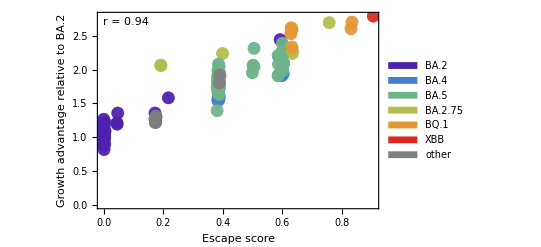

```mathematica
fig=ListPlot[Map[{#}&,escapeGAPairs],PlotTheme->"FullAxes",Frame->{True,True,False,False},PlotMarkers->{"•",Medium},PlotStyle->Map[Directive[Opacity[0.75],#]&,pangoLineages/.pangoColorMapping],FrameLabel->{"Escape score","Growth advantage relative to BA.2"},Epilog->{Directive[FontSize->11,FontFamily->"Helvetica"],Text["r = "<>ToString[Round[escapeGACorr,0.01]],Scaled[{0.02,0.95}],{-1,0}]},PlotLegends->legendPanel]
```

```mathematica
Export["figures/escape_growth_advantage_correlation.png",fig,"PNG",ImageResolution->300]
```

figures/escape_growth_advantage_correlation.png

### Binding

```mathematica
bindingGAPairs=Table[{(pangoLineage/.pangoBindingMapping)+RandomVariate[NormalDistribution[0,0.002]],pangoLineage/.pangoGAMapping},{pangoLineage,pangoLineages}];
```

```mathematica
bindingGACorr=Correlation[bindingGAPairs[[All,1]],bindingGAPairs[[All,2]]]
```

0.845577

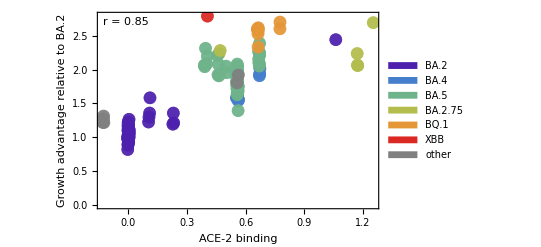

```mathematica
fig=ListPlot[Map[{#}&,bindingGAPairs],PlotTheme->"FullAxes",Frame->{True,True,False,False},PlotMarkers->{"•",Medium},PlotStyle->Map[Directive[Opacity[0.75],#]&,pangoLineages/.pangoColorMapping],FrameLabel->{"ACE-2 binding","Growth advantage relative to BA.2"},Epilog->{Directive[FontSize->11,FontFamily->"Helvetica"],Text["r = "<>ToString[Round[bindingGACorr,0.01]],Scaled[{0.02,0.95}],{-1,0}]},PlotLegends->legendPanel]
```

```mathematica
Export["figures/binding_growth_advantage_correlation.png",fig,"PNG",ImageResolution->300]
```

figures/binding_growth_advantage_correlation.png

### RBD mutations

```mathematica
rbdGAPairs=Table[{(pangoLineage/.pangoRBDMapping)+RandomVariate[NormalDistribution[0,0.002]],pangoLineage/.pangoGAMapping},{pangoLineage,pangoLineages}];
```

```mathematica
rbdGACorr=Correlation[rbdGAPairs[[All,1]],rbdGAPairs[[All,2]]]
```

0.955084

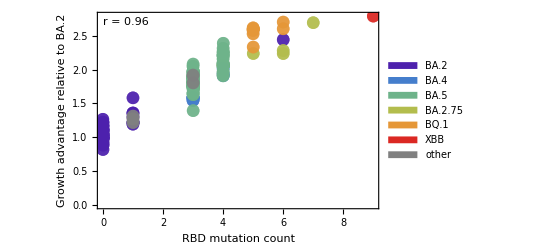

```mathematica
fig=ListPlot[Map[{#}&,rbdGAPairs],PlotTheme->"FullAxes",Frame->{True,True,False,False},PlotMarkers->{"•",Medium},PlotStyle->Map[Directive[Opacity[0.75],#]&,pangoLineages/.pangoColorMapping],FrameLabel->{"RBD mutation count","Growth advantage relative to BA.2"},Epilog->{Directive[FontSize->11,FontFamily->"Helvetica"],Text["r = "<>ToString[Round[rbdGACorr,0.01]],Scaled[{0.02,0.95}],{-1,0}]},PlotLegends->legendPanel]
```

```mathematica
Export["figures/rbd_growth_advantage_correlation.png",fig,"PNG",ImageResolution->300]
```

figures/rbd_growth_advantage_correlation.png

### Non-RBD spike mutations

```mathematica
spikeGAPairs=Table[{(pangoLineage/.pangoSpikeMapping)+RandomVariate[NormalDistribution[0,0.002]],pangoLineage/.pangoGAMapping},{pangoLineage,pangoLineages}];
```

```mathematica
spikeGACorr=Correlation[spikeGAPairs[[All,1]],spikeGAPairs[[All,2]]]
```

0.722536

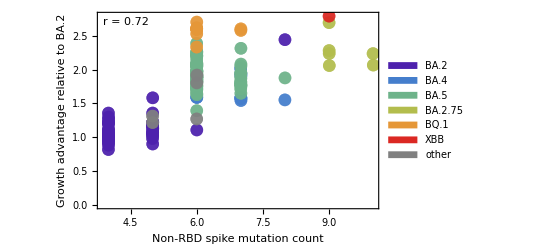

```mathematica
fig=ListPlot[Map[{#}&,spikeGAPairs],PlotTheme->"FullAxes",Frame->{True,True,False,False},PlotMarkers->{"•",Medium},PlotStyle->Map[Directive[Opacity[0.75],#]&,pangoLineages/.pangoColorMapping],FrameLabel->{"Non-RBD spike mutation count","Growth advantage relative to BA.2"},Epilog->{Directive[FontSize->11,FontFamily->"Helvetica"],Text["r = "<>ToString[Round[spikeGACorr,0.01]],Scaled[{0.02,0.95}],{-1,0}]},PlotLegends->legendPanel]
```

```mathematica
Export["figures/spike_growth_advantage_correlation.png",fig,"PNG",ImageResolution->300]
```

figures/spike_growth_advantage_correlation.png

### Non-spike mutations

```mathematica
nonSpikeGAPairs=Table[{(pangoLineage/.pangoNonSpikeMapping)+RandomVariate[NormalDistribution[0,0.002]],pangoLineage/.pangoGAMapping},{pangoLineage,pangoLineages}];
```

```mathematica
nonSpikeGACorr=Correlation[nonSpikeGAPairs[[All,1]],nonSpikeGAPairs[[All,2]]]
```

0.642798

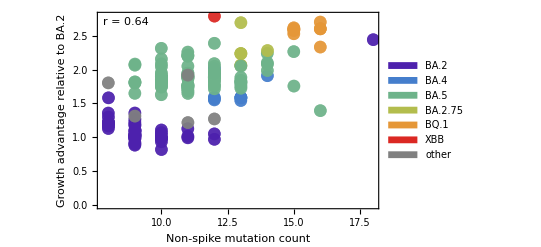

```mathematica
fig=ListPlot[Map[{#}&,nonSpikeGAPairs],PlotTheme->"FullAxes",Frame->{True,True,False,False},PlotMarkers->{"•",Medium},PlotStyle->Map[Directive[Opacity[0.75],#]&,pangoLineages/.pangoColorMapping],FrameLabel->{"Non-spike mutation count","Growth advantage relative to BA.2"},Epilog->{Directive[FontSize->11,FontFamily->"Helvetica"],Text["r = "<>ToString[Round[nonSpikeGACorr,0.01]],Scaled[{0.02,0.95}],{-1,0}]},PlotLegends->legendPanel]
```

```mathematica
Export["figures/non_spike_growth_advantage_correlation.png",fig,"PNG",ImageResolution->300]
```

figures/non_spike_growth_advantage_correlation.png

## Multiple regression

Predict continuous variable growth advantage Y from escape X_1, binding X_2, RBD mutation count X_3, non-RBD spike mutation count X_4 and non-spike mutation count X_5,

```mathematica
regressionData=Table[{pangoLineage/.pangoEscapeMapping,pangoLineage/.pangoBindingMapping,pangoLineage/.pangoRBDMapping,pangoLineage/.pangoSpikeMapping,pangoLineage/.pangoNonSpikeMapping,pangoLineage/.pangoGAMapping},{pangoLineage,pangoLineages}];
```

```mathematica
lm=LinearModelFit[regressionData,{betaEscape,betaBinding,betaRBD,betaSpike,betaNonSpike},{betaEscape,betaBinding,betaRBD,betaSpike,betaNonSpike}]
```

FittedModel[1.24031+0.256892 betaBinding+0.513702 betaEscape-«22» betaNonSpike+0.177761 betaRBD-0.0405691 betaSpike]

```mathematica
lm["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 1.24031 | 0.104783 | 11.837 | 1.79488×10^-23
betaEscape | 0.513702 | 0.194011 | 2.6478 | 0.00893394
betaBinding | 0.256892 | 0.0734012 | 3.49984 | 0.000607044
betaRBD | 0.177761 | 0.0312681 | 5.68506 | 6.2636×10^-8
betaSpike | -0.0405691 | 0.0166084 | -2.44269 | 0.0156946
betaNonSpike | -0.00283138 | 0.00685411 | -0.413093 | 0.680106